## Introduction

Make pics for paper

## Main sim

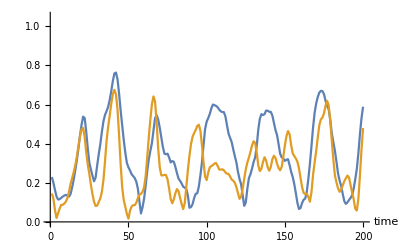

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={0.5,0.5};
{e,b}={1.1,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.9,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin={Table[2 Pi i / (n-1),{i,0,n-1}]//N,RandomReal[{0,2π},n]};
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]

ListPlot[{Abs[Wp],Abs[Wm]},Joined->True,AxesLabel->{"time"},LabelStyle->15,PlotRange->{0,1.05}]
```

## Bistability

### Old

```mathematica
(*Preamble*)
data1=Table[
{dt,n,T}={0.5,200,200}; 
{J}={1};
{e,b}={0.8,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{k,Sp,Sm},
{k,k1,k2,dk}
];

(*Preamble*)
data2=Table[
{dt,n,T}={0.5,200,100}; 
{J}={1};
{e,b}={0.8,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{k,Sp,Sm},
{k,k1,k2,dk}
];
```

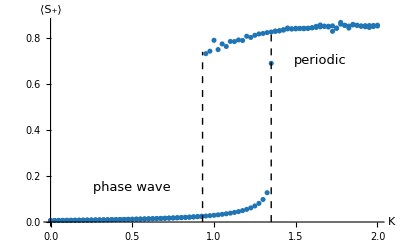

```mathematica
{pa,pb}={0.93,1.35};
p1=ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["K",18,Italic],Style["⟨S_+⟩",18,Italic]},LabelStyle->15,PlotStyle->{ColorData[99,"ColorList"]},
Epilog->{
Dashed,Line[{{pa,0},{pa,0.74}}],Line[{{pb,0},{pb,0.82}}],
Text[Style["phase wave",13],{0.5,0.15}],
Text[Style["periodic",13],{1.65,0.7}]
}]
SetDirectory[NotebookDirectory[]];
Export["figures/hysteresis.png",p1];
```

### New S(K)

```mathematica
{k1,k2,dk}={0.5,1.4,0.01};

(*Preamble*)
data1=Table[
{dt,n,T}={0.5,300,200}; 
{J}={k};
{e,b}={0.8,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{k,Sp,Sm},
{k,k1,k2,dk}
];

(*Preamble*)
data2=Table[
{dt,n,T}={0.5,200,100}; 
{J}={1};
{e,b}={0.8,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{k,Sp,Sm},
{k,k1,k2,dk}
];
```

#### Save data

```mathematica
data1={{0.5,0.0057007306736598165,1.},{0.51,0.005782874160178795,1.},{0.52,0.005867419660034285,1.},{0.53,0.005954474106911049,1.},{0.54,0.00604415087855718,1.},{0.55,0.006136570289711538,1.},{0.56,0.006231860131035073,1.},{0.5700000000000001,0.006330156259092654,1.},{0.58,0.006431603243089891,1.},{0.59,0.0065363550748956945,1.},{0.6,0.006644575949692663,1.},{0.61,0.006756441125536943,1.},{0.62,0.006872137871372762,1.},{0.63,0.006991866514246258,1.},{0.64,0.007115841598088976,1.},{0.65,0.0072442931682254,1.},{0.66,0.007377468197708266,1.},{0.67,0.0075156321742578976,1.},{0.6799999999999999,0.007659070869197043,1.},{0.69,0.0078080923132725875,1.},{0.7,0.007963029008221122,1.},{0.71,0.008124240407481857,1.},{0.72,0.008292115705165696,1.},{0.73,0.008467076978989763,1.},{0.74,0.008649582740679567,1.},{0.75,0.008840131956946396,1.},{0.76,0.009039268615544736,1.},{0.77,0.009247586924680069,1.},{0.78,0.009465737250874299,1.},{0.79,0.009694432920677057,1.},{0.8,0.009934458036864708,1.},{0.81,0.010186676490279671,1.},{0.8200000000000001,0.010452042386813213,1.},{0.8300000000000001,0.010731612156104114,1.},{0.8400000000000001,0.011026558667877162,1.},{0.8500000000000001,0.011338187756232304,1.},{0.86,0.01166795764613861,1.},{0.87,0.012017501896484989,1.},{0.88,0.01238865662762377,1.},{0.89,0.012783492999699218,1.},{0.9,0.013204356166886986,1.},{0.91,0.013653912272088247,1.},{0.9199999999999999,0.014135205494604342,1.},{0.9299999999999999,0.014651727758325399,1.},{0.94,0.015207504555672364,1.},{0.95,0.015807201352866087,1.},{0.96,0.016456256787275192,1.},{0.97,0.017161050507760126,1.},{0.98,0.01792911774018813,1.},{0.99,0.01876942455101128,1.},{1.,0.019692729636498717,1.},{1.01,0.02071205457180432,1.},{1.02,0.021843329210973803,1.},{1.03,0.023106269472489536,1.},{1.04,0.024525466313563442,1.},{1.05,0.02613250431389805,1.},{1.06,0.027967724414555414,1.},{1.07,0.03008499118788548,1.},{1.08,0.032555789596497416,1.},{1.0899999999999999,0.035482555712702174,1.},{1.1,0.0390068041433333,1.},{1.1099999999999999,0.0433495807138759,1.},{1.12,0.04880331705466809,1.},{1.13,0.056009264012879326,1.},{1.1400000000000001,0.06623259662011094,1.},{1.15,0.0822489026115021,1.},{1.1600000000000001,0.7557800433028059,1.},{1.17,0.8272903135386092,1.},{1.1800000000000002,0.830724171684383,1.},{1.19,0.8322762960195877,1.},{1.2000000000000002,0.833428584994928,1.},{1.21,0.8345213256981479,1.},{1.22,0.836284511782687,0.9999999487516199},{1.23,0.8370060382011497,1.},{1.24,0.8383591826806254,0.9999670745436413},{1.25,0.8393272203608532,1.},{1.26,0.8410106430738377,0.9999999999999941},{1.27,0.8421859905569461,0.9999999999817789},{1.28,0.8432781024635805,0.999999999996476},{1.29,0.8442634842942811,0.9999999999837433},{1.3,0.8446297798167048,0.999999999933484},{1.31,0.8313585965919176,0.8522212375423259},{1.32,0.8464230264629343,0.9999999853545257},{1.33,0.8477570178723886,0.9999999999999722},{1.3399999999999999,0.8353149566328112,0.8658371753797633},{1.35,0.8492878085163296,0.9999955759841025},{1.3599999999999999,0.8416217413779156,0.8704950443540419},{1.37,0.8417809430524751,0.8657804408339902},{1.38,0.8509805219265135,0.9999985715040594},{1.3900000000000001,0.8467898022234432,0.8702376825496336},{1.4,0.8522626135244319,0.9997661275716508}};
```

```mathematica
data2={{0.5,0.0120050882489539,0.999998770439927},{0.51,0.012174730485044674,0.999998794462483},{0.52,0.012347937061774783,0.9999988187443914},{0.53,0.012524821652542198,0.9999988432860583},{0.54,0.012705502754003442,0.9999988680875824},{0.55,0.012890104255311806,0.9999988931486531},{0.56,0.013078755200328918,0.9999989184686249},{0.5700000000000001,0.013271590946594752,0.9999989440462994},{0.58,0.013468751858502962,0.999998969880199},{0.59,0.013670386056557843,0.9999989959680458},{0.6,0.013876647958383873,0.9999990223070689},{0.61,0.014087698778458557,0.9999990488938996},{0.62,0.014303706962818807,0.9999990757244843},{0.63,0.014524850871690555,0.999999102793672},{0.64,0.014751317650047174,0.9999991300954141},{0.65,0.014983294820939463,0.9999991576238494},{0.66,0.015220997198874623,0.9999991853696231},{0.67,0.01546463439476547,0.9999992133242612},{0.6799999999999999,0.015714432370538406,0.9999992414772004},{0.69,0.01597062622663194,0.9999992698166584},{0.7,0.016233483701059117,0.9999992983271387},{0.71,0.016503227154582068,0.999999326997213},{0.72,0.016780169204335227,0.9999993558058171},{0.73,0.017064591876005515,0.9999993847342055},{0.74,0.017356849724652346,0.9999994137565977},{0.75,0.01765717877912497,0.9999994428551214},{0.76,0.017965966923876964,0.9999994719981383},{0.77,0.018283523011120333,0.9999995011575901},{0.78,0.018610424760995836,0.9999995302865727},{0.79,0.01894692872732649,0.9999995593554813},{0.8,0.01929340156613592,0.9999995883231579},{0.81,0.019650647827137734,0.9999996171242717},{0.8200000000000001,0.0200183610645995,0.9999996457382184},{0.8300000000000001,0.02039788740936235,0.9999996740678023},{0.8400000000000001,0.020789964444768355,0.9999997020418101},{0.8500000000000001,0.02119459803574172,0.9999997296049088},{0.86,0.021611851948682807,0.9999997566838003},{0.87,0.022043326045234218,0.999999783155715},{0.88,0.022490391320017577,0.999999808903494},{0.89,0.022954187262990484,0.9999998338085283},{0.9,0.02343588967886982,0.9999998577407978},{0.91,0.023936231212507167,0.9999998805611865},{0.9199999999999999,0.02444732059917431,0.9999999021841939},{0.9299999999999999,0.02498921689757642,0.9999999222447022},{0.94,0.025580506520478215,0.99999994050146},{0.95,0.02625369536468225,0.9999999567256753},{0.96,0.7325622765964263,0.871245204085517},{0.97,0.7624337262343365,0.8877498958544614},{0.98,0.7810006212260124,0.9417525569234956},{0.99,0.7866266224522833,0.9849644642404863},{1.,0.7894396299174398,0.999999818252122},{1.01,0.7896710141225155,0.9822845436841534},{1.02,0.754312256001423,0.8637234119907485},{1.03,0.7850882130808243,0.9422423777328042},{1.04,0.7501191586596374,0.8644625297048026},{1.05,0.7731038123802502,0.9294812760444053},{1.06,0.782813780145211,0.920071781299541},{1.07,0.7671927815643128,0.8540042794695635},{1.08,0.7675336759604738,0.8771126398107993},{1.0899999999999999,0.7830261212250798,0.9132071591813274},{1.1,0.7811222360658954,0.8911838327645272},{1.1099999999999999,0.7833251403257057,0.8598038531699876},{1.12,0.7848272085751621,0.846120046691724},{1.13,0.7770316803628878,0.8419522372352182},{1.1400000000000001,0.785561219368667,0.8674435841674454},{1.15,0.7909250222770936,0.8924839253117766},{1.1600000000000001,0.7924306001782313,0.8791384084374458},{1.17,0.7869027285345629,0.8499062183979055},{1.1800000000000002,0.7901213308693865,0.8388505322381915},{1.19,0.8002402210201003,0.8283388663273938},{1.2000000000000002,0.8074933392371232,0.8227982293876233},{1.21,0.8085250232452963,0.8173929822118302},{1.22,0.8041642687812349,0.8152777861375944},{1.23,0.8053261064571005,0.8169397560291427},{1.24,0.8086426786511298,0.8286840284316233},{1.25,0.8114474347812591,0.8350072465365534},{1.26,0.8110852064279124,0.8445382198009451},{1.27,0.8120671423735087,0.8564340107419648},{1.28,0.8169337656509489,0.8577346629712965},{1.29,0.819390519739095,0.8606218060044646},{1.3,0.8202911332974216,0.87128675899989},{1.31,0.8213480582650251,0.8624058300393204},{1.32,0.8225994468029617,0.8612074777137422},{1.33,0.8223737599473081,0.8629694168239449},{1.3399999999999999,0.8239294460343656,0.861287613918605},{1.35,0.825933129826548,0.8676878915638891},{1.3599999999999999,0.8276158567201555,0.8717728826072776},{1.37,0.8289220065215532,0.8732670757439569},{1.38,0.8309761465548624,0.8722527138104887},{1.3900000000000001,0.83288136841515,0.8566853585243327},{1.4,0.8354625817426724,0.8392866066056538}};
```

#### Plot data

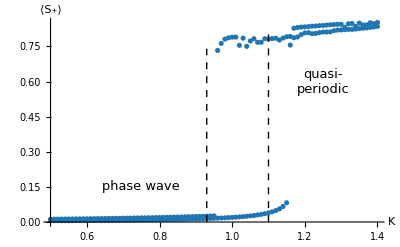

```mathematica
{pa,pb}={0.93,1.1};
p1=ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["K",18,Italic],Style["⟨S_+⟩",18,Italic]},LabelStyle->15,PlotStyle->{ColorData[99,"ColorList"]},PlotRange->{{0.5,1.4},Automatic},
Epilog->{
Dashed,Line[{{pa,0},{pa,0.74}}],Line[{{pb,0},{pb,0.82}}],
Text[Style["phase wave",13],{0.75,0.15}],
Text[Style["quasi-\nperiodic",13],{1.25,0.6}]
}]
SetDirectory[NotebookDirectory[]];
Export["figures/hysteresis.png",p1];
```

### New S(E)

```mathematica
{e1,e2,de}={0.7,0.9,0.005};

(*Preamble*)
data1=Table[
{dt,n,T}={0.5,300,200}; 
{K,k}={1,1};
{b}={1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{e,Sp,Sm},
{e,e1,e2,de}
];

(*Preamble*)
data2=Table[
{dt,n,T}={0.5,300,200}; 
{K,k}={1,1};
{b}={1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{e,Sp,Sm},
{e,e1,e2,de}
];
```

#### Save data

```mathematica
data1={{0.5,0.0057007306736598165,1.},{0.51,0.005782874160178795,1.},{0.52,0.005867419660034285,1.},{0.53,0.005954474106911049,1.},{0.54,0.00604415087855718,1.},{0.55,0.006136570289711538,1.},{0.56,0.006231860131035073,1.},{0.5700000000000001,0.006330156259092654,1.},{0.58,0.006431603243089891,1.},{0.59,0.0065363550748956945,1.},{0.6,0.006644575949692663,1.},{0.61,0.006756441125536943,1.},{0.62,0.006872137871372762,1.},{0.63,0.006991866514246258,1.},{0.64,0.007115841598088976,1.},{0.65,0.0072442931682254,1.},{0.66,0.007377468197708266,1.},{0.67,0.0075156321742578976,1.},{0.6799999999999999,0.007659070869197043,1.},{0.69,0.0078080923132725875,1.},{0.7,0.007963029008221122,1.},{0.71,0.008124240407481857,1.},{0.72,0.008292115705165696,1.},{0.73,0.008467076978989763,1.},{0.74,0.008649582740679567,1.},{0.75,0.008840131956946396,1.},{0.76,0.009039268615544736,1.},{0.77,0.009247586924680069,1.},{0.78,0.009465737250874299,1.},{0.79,0.009694432920677057,1.},{0.8,0.009934458036864708,1.},{0.81,0.010186676490279671,1.},{0.8200000000000001,0.010452042386813213,1.},{0.8300000000000001,0.010731612156104114,1.},{0.8400000000000001,0.011026558667877162,1.},{0.8500000000000001,0.011338187756232304,1.},{0.86,0.01166795764613861,1.},{0.87,0.012017501896484989,1.},{0.88,0.01238865662762377,1.},{0.89,0.012783492999699218,1.},{0.9,0.013204356166886986,1.},{0.91,0.013653912272088247,1.},{0.9199999999999999,0.014135205494604342,1.},{0.9299999999999999,0.014651727758325399,1.},{0.94,0.015207504555672364,1.},{0.95,0.015807201352866087,1.},{0.96,0.016456256787275192,1.},{0.97,0.017161050507760126,1.},{0.98,0.01792911774018813,1.},{0.99,0.01876942455101128,1.},{1.,0.019692729636498717,1.},{1.01,0.02071205457180432,1.},{1.02,0.021843329210973803,1.},{1.03,0.023106269472489536,1.},{1.04,0.024525466313563442,1.},{1.05,0.02613250431389805,1.},{1.06,0.027967724414555414,1.},{1.07,0.03008499118788548,1.},{1.08,0.032555789596497416,1.},{1.0899999999999999,0.035482555712702174,1.},{1.1,0.0390068041433333,1.},{1.1099999999999999,0.0433495807138759,1.},{1.12,0.04880331705466809,1.},{1.13,0.056009264012879326,1.},{1.1400000000000001,0.06623259662011094,1.},{1.15,0.0822489026115021,1.},{1.1600000000000001,0.7557800433028059,1.},{1.17,0.8272903135386092,1.},{1.1800000000000002,0.830724171684383,1.},{1.19,0.8322762960195877,1.},{1.2000000000000002,0.833428584994928,1.},{1.21,0.8345213256981479,1.},{1.22,0.836284511782687,0.9999999487516199},{1.23,0.8370060382011497,1.},{1.24,0.8383591826806254,0.9999670745436413},{1.25,0.8393272203608532,1.},{1.26,0.8410106430738377,0.9999999999999941},{1.27,0.8421859905569461,0.9999999999817789},{1.28,0.8432781024635805,0.999999999996476},{1.29,0.8442634842942811,0.9999999999837433},{1.3,0.8446297798167048,0.999999999933484},{1.31,0.8313585965919176,0.8522212375423259},{1.32,0.8464230264629343,0.9999999853545257},{1.33,0.8477570178723886,0.9999999999999722},{1.3399999999999999,0.8353149566328112,0.8658371753797633},{1.35,0.8492878085163296,0.9999955759841025},{1.3599999999999999,0.8416217413779156,0.8704950443540419},{1.37,0.8417809430524751,0.8657804408339902},{1.38,0.8509805219265135,0.9999985715040594},{1.3900000000000001,0.8467898022234432,0.8702376825496336},{1.4,0.8522626135244319,0.9997661275716508}};
```

```mathematica
data2={{0.5,0.0120050882489539,0.999998770439927},{0.51,0.012174730485044674,0.999998794462483},{0.52,0.012347937061774783,0.9999988187443914},{0.53,0.012524821652542198,0.9999988432860583},{0.54,0.012705502754003442,0.9999988680875824},{0.55,0.012890104255311806,0.9999988931486531},{0.56,0.013078755200328918,0.9999989184686249},{0.5700000000000001,0.013271590946594752,0.9999989440462994},{0.58,0.013468751858502962,0.999998969880199},{0.59,0.013670386056557843,0.9999989959680458},{0.6,0.013876647958383873,0.9999990223070689},{0.61,0.014087698778458557,0.9999990488938996},{0.62,0.014303706962818807,0.9999990757244843},{0.63,0.014524850871690555,0.999999102793672},{0.64,0.014751317650047174,0.9999991300954141},{0.65,0.014983294820939463,0.9999991576238494},{0.66,0.015220997198874623,0.9999991853696231},{0.67,0.01546463439476547,0.9999992133242612},{0.6799999999999999,0.015714432370538406,0.9999992414772004},{0.69,0.01597062622663194,0.9999992698166584},{0.7,0.016233483701059117,0.9999992983271387},{0.71,0.016503227154582068,0.999999326997213},{0.72,0.016780169204335227,0.9999993558058171},{0.73,0.017064591876005515,0.9999993847342055},{0.74,0.017356849724652346,0.9999994137565977},{0.75,0.01765717877912497,0.9999994428551214},{0.76,0.017965966923876964,0.9999994719981383},{0.77,0.018283523011120333,0.9999995011575901},{0.78,0.018610424760995836,0.9999995302865727},{0.79,0.01894692872732649,0.9999995593554813},{0.8,0.01929340156613592,0.9999995883231579},{0.81,0.019650647827137734,0.9999996171242717},{0.8200000000000001,0.0200183610645995,0.9999996457382184},{0.8300000000000001,0.02039788740936235,0.9999996740678023},{0.8400000000000001,0.020789964444768355,0.9999997020418101},{0.8500000000000001,0.02119459803574172,0.9999997296049088},{0.86,0.021611851948682807,0.9999997566838003},{0.87,0.022043326045234218,0.999999783155715},{0.88,0.022490391320017577,0.999999808903494},{0.89,0.022954187262990484,0.9999998338085283},{0.9,0.02343588967886982,0.9999998577407978},{0.91,0.023936231212507167,0.9999998805611865},{0.9199999999999999,0.02444732059917431,0.9999999021841939},{0.9299999999999999,0.02498921689757642,0.9999999222447022},{0.94,0.025580506520478215,0.99999994050146},{0.95,0.02625369536468225,0.9999999567256753},{0.96,0.7325622765964263,0.871245204085517},{0.97,0.7624337262343365,0.8877498958544614},{0.98,0.7810006212260124,0.9417525569234956},{0.99,0.7866266224522833,0.9849644642404863},{1.,0.7894396299174398,0.999999818252122},{1.01,0.7896710141225155,0.9822845436841534},{1.02,0.754312256001423,0.8637234119907485},{1.03,0.7850882130808243,0.9422423777328042},{1.04,0.7501191586596374,0.8644625297048026},{1.05,0.7731038123802502,0.9294812760444053},{1.06,0.782813780145211,0.920071781299541},{1.07,0.7671927815643128,0.8540042794695635},{1.08,0.7675336759604738,0.8771126398107993},{1.0899999999999999,0.7830261212250798,0.9132071591813274},{1.1,0.7811222360658954,0.8911838327645272},{1.1099999999999999,0.7833251403257057,0.8598038531699876},{1.12,0.7848272085751621,0.846120046691724},{1.13,0.7770316803628878,0.8419522372352182},{1.1400000000000001,0.785561219368667,0.8674435841674454},{1.15,0.7909250222770936,0.8924839253117766},{1.1600000000000001,0.7924306001782313,0.8791384084374458},{1.17,0.7869027285345629,0.8499062183979055},{1.1800000000000002,0.7901213308693865,0.8388505322381915},{1.19,0.8002402210201003,0.8283388663273938},{1.2000000000000002,0.8074933392371232,0.8227982293876233},{1.21,0.8085250232452963,0.8173929822118302},{1.22,0.8041642687812349,0.8152777861375944},{1.23,0.8053261064571005,0.8169397560291427},{1.24,0.8086426786511298,0.8286840284316233},{1.25,0.8114474347812591,0.8350072465365534},{1.26,0.8110852064279124,0.8445382198009451},{1.27,0.8120671423735087,0.8564340107419648},{1.28,0.8169337656509489,0.8577346629712965},{1.29,0.819390519739095,0.8606218060044646},{1.3,0.8202911332974216,0.87128675899989},{1.31,0.8213480582650251,0.8624058300393204},{1.32,0.8225994468029617,0.8612074777137422},{1.33,0.8223737599473081,0.8629694168239449},{1.3399999999999999,0.8239294460343656,0.861287613918605},{1.35,0.825933129826548,0.8676878915638891},{1.3599999999999999,0.8276158567201555,0.8717728826072776},{1.37,0.8289220065215532,0.8732670757439569},{1.38,0.8309761465548624,0.8722527138104887},{1.3900000000000001,0.83288136841515,0.8566853585243327},{1.4,0.8354625817426724,0.8392866066056538}};
```

#### Plot data

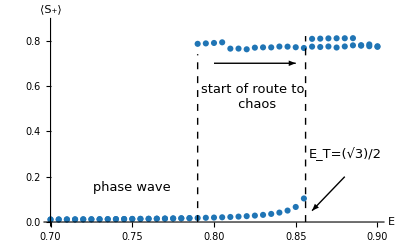

```mathematica
{pa,pb}={0.79,√3/2-0.01};
p1=ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["E",18,Italic],Style["⟨S_+⟩",18,Italic]},LabelStyle->15,PlotStyle->{ColorData[99,"ColorList"]},PlotRange->{{0.7,0.9},{0,0.88}},
Epilog->{
Arrow[{{0.8,0.7},{0.85,0.7}}],
Arrow[{{0.88,0.2},{0.86,0.05}}],
Dashed,Line[{{pa,0},{pa,0.74}}],Line[{{pb,0},{pb,0.82}}],
Text[Style["phase wave",13],{0.75,0.15}],
Text[Style["start of route to \n chaos",13],{0.825,0.55}],
Text[Style["E_T=(√3)/2",13],{0.88,0.3}]
}]
SetDirectory[NotebookDirectory[]];
Export["figures/hysteresisE.png",p1];
```

## Split phase wave

### Main

```mathematica
(*Preamble*)
{dt,n,T}={0.1,200,500}; 
{J,k}={-50,-50};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]
```

$Aborted

```mathematica
run2[k1_,n_,T_]:=Block[{dt,J,e,b,b1,b2,Ex,Eθ,z0,pin,znew,z00,Wp,Wp1,Wm1,Wm,t,NT,temp,xi,eta,x,θ,k,theta},

(*Preamble*)
{dt}={0.1}; 
{J,k}={k1,k1};
{e,b}={0,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];

(*Stuff here*)
{x,θ}=znew;
temp={Mod[x+θ,2π]-π,Mod[x-θ,2π]-π}ᵀ;
temp=Sort[temp];
{xi,eta}={temp[[All,1]],temp[[All,2]]};
Return[{Mod[x,2π]-π,Mod[θ,2π]-π,xi,eta,Abs[Wp][[-1]],Abs[Wm][[-1]]}]
]
```

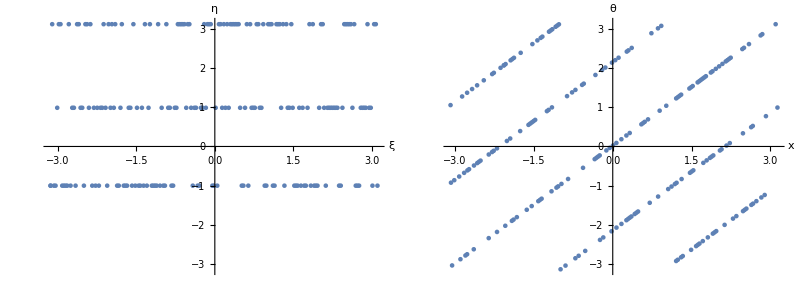

{{0.,76},{4.1,35},{2.,43},{2.1,45}}

{0.38,4.1,0.000190268,0.0278524}

```mathematica
n=200;
{x,theta,xi,eta,Sp,Sm}=run2[-50,n,1000];
p1=ListPlot[{xi,eta}ᵀ,PlotRange->{-π,π},AxesLabel->{"ξ","η"},LabelStyle->15,ImageSize->Medium];
p2=ListPlot[{x,theta}ᵀ,PlotRange->{-π,π},AxesLabel->{"x","θ"},LabelStyle->15,ImageSize->Medium];
Grid[{{p1,p2}}]
Tally[Mod[Round[Abs[Differences[eta]],0.1],6.3]]
temp=Tally[Mod[Round[Abs[Differences[eta]],0.1],6.3]];
delta=Max[temp[[All,1]]];
p=N[Max[temp[[All,2]]]/n];
{p,delta,Sp,Sm}
```

#### Iterate

```mathematica
n=50;
realdata=ParallelTable[
{x,theta,xi,eta,Sp,Sm}=run2[k,n,500];
temp=Tally[Mod[Round[Abs[Differences[eta]],0.1],6.3]];
delta=Max[temp[[All,1]]];
p=N[Max[temp[[All,2]]]/n];
{k,p,delta,Sm},
{k,0,-10,-0.1}
];
```

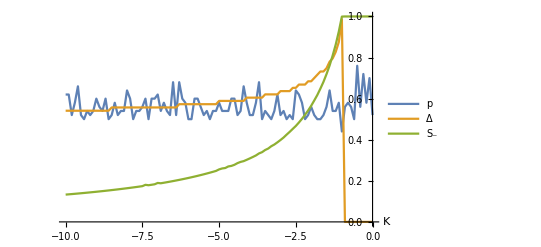

```mathematica
ListPlot[{realdata[[All,{1,2}]],{realdata[[All,1]],realdata[[All,3]]/(2π)}ᵀ,realdata[[All,{1,4}]]},Joined->True,PlotRange->All,AxesLabel->{"K"},PlotLegends->{"p","Δ","S_-"}]
```

### Find state

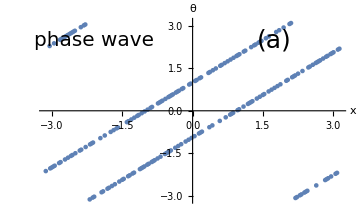

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={-2,-2};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p1=ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["phase wave",20],{-2.1,2.5}],Text[Style["(a)",25],{1.75,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

```mathematica
Dimensions[x]
```

{200}

```mathematica
temp={Mod[x+θ,2π]-π,Mod[x-θ,2π]-π}ᵀ;
temp=Sort[temp];
{xi,eta}={temp[[All,1]],temp[[All,2]]};
```

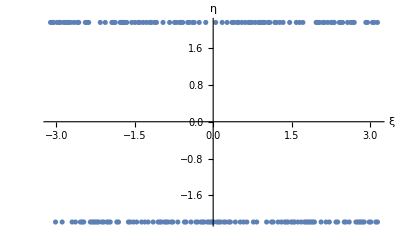

```mathematica
ListPlot[{xi,eta}ᵀ,AxesLabel->{"ξ","η"}]
```

### S(K)

#### Make data

```mathematica
dataReal=ParallelTable[
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.1,200,100}; 
{J,k}={K,K};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

cutoff=Round[0.5 Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
(*If[Sp≤Sm,{Sp,Sm}={Sm,Sp}];*)
{K,Sp,Sm},
{K,-5,5,0.1}
];
```

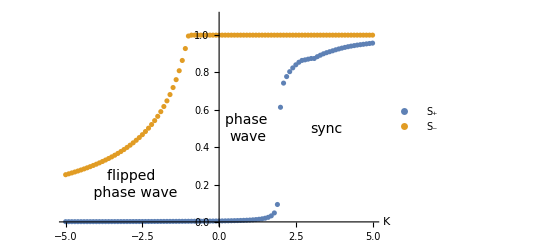

figures/order-pars-undriven.png

```mathematica
p1b=ListPlot[{dataReal[[All,{1,2}]],dataReal[[All,{1,3}]]},AxesLabel->{Style["K",22,Italic]},PlotLegends->{Style["S_+",19],Style["S_-",19]},LabelStyle->16,PlotRange->{0,1.1},Epilog->{Dashed,(*Line[{{-1,0},{-1,1}}],Line[{{2,0},{2,1}}],*)Text[Style["sync",14],{3.5,0.5}],Text[Style["phase \nwave",14],{0.95,0.5}],Text[Style["flipped \n phase wave",14],{-2.8,0.2}]}]
SetDirectory[NotebookDirectory[]];
Export["figures/order-pars-undriven.png",p1b]
```

#### Gourab’s Ansatz

{0,0.540302}

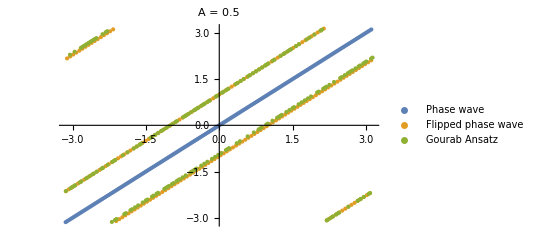

```mathematica
{A,n}={0.5,200};
α=Table[(2π i)/n,{i,0,n-1}];
data=Table[{α[[i]]+(-1)^i A,α[[i]]+(-1)^(i-1)A}//mod,{i,1,n}];
{x,θ}={data[[All,1]],data[[All,2]]};
{sp1,sm1}={N[Total[Exp[ⅈ(x+θ)]]/Length[x]],N[Total[Exp[ⅈ(x-θ)]]/Length[x]]}//Chop
{xreal,θreal}=znew;
ListPlot[{{α,α}ᵀ//mod,data,{xreal,θreal}ᵀ//mod},PlotLegends->{"Phase wave","Flipped phase wave","Gourab Ansatz"},PlotLabel->"A = 0.5",LabelStyle->15]
```

Perfect!

#### Solve self consistency equations

```mathematica
Sin[xreal-θreal]
```

{-0.84245,0.806711,0.806711,0.806712,0.806712,0.806712,-0.842451,-0.842451,-0.842452,0.806714,-0.842452,0.806715,0.806715,-0.842454,-0.842454,0.806717,-0.842455,0.806718,0.806719,-0.842456,-0.842456,-0.842456,-0.842457,0.80672,0.80672,-0.842457,-0.842457,0.80672,0.80672,-0.842456,0.806719,-0.842456,0.806718,-0.842455,-0.842455,0.806717,-0.842454,0.806716,0.806715,-0.842453,-0.842452,0.806714,0.806713,-0.842451,0.806712,0.806712,-0.84245,-0.84245,-0.84245,0.806711,0.806711,0.806711,0.806711,-0.84245,0.806712,0.806712,-0.842451,0.806713,0.806713,0.806714,-0.842453,0.806715,-0.842453,0.806716,-0.842454,-0.842455,0.806718,0.806718,0.806719,0.806719,0.806719,-0.842456,-0.842457,0.80672,-0.842457,0.80672,-0.842457,0.80672,-0.842457,-0.842456,0.806719,-0.842456,0.806718,-0.842455,0.806717,-0.842454,0.806716,-0.842454,-0.842453,0.806715,0.806714,0.806714,-0.842452,-0.842451,-0.842451,-0.842451,0.806712,-0.84245,0.806711,-0.84245,-0.84245,-0.84245,-0.84245,0.806712,-0.842451,-0.842451,-0.842451,0.806713,-0.842452,-0.842452,0.806715,0.806715,0.806716,-0.842454,-0.842454,0.806717,0.806718,-0.842455,-0.842456,0.806719,-0.842456,-0.842457,0.80672,0.80672,0.80672,0.80672,-0.842457,-0.842457,0.80672,-0.842456,0.806719,-0.842456,0.806718,0.806718,-0.842455,-0.842454,0.806716,-0.842453,0.806715,-0.842453,0.806714,-0.842452,0.806713,-0.842451,0.806712,-0.842451,-0.84245,-0.84245,0.806711,0.806711,-0.84245,-0.84245,0.806712,0.806712,0.806712,-0.842451,0.806713,-0.842452,-0.842452,0.806714,-0.842453,-0.842453,-0.842454,0.806716,0.806717,-0.842455,0.806718,-0.842456,0.806719,0.806719,0.806719,0.80672,-0.842457,0.80672,-0.842457,0.80672,0.80672,-0.842457,0.80672,0.806719,0.806719,-0.842456,-0.842455,0.806718,0.806717,-0.842454,-0.842454,0.806715,-0.842453,-0.842452,0.806714,-0.842452,-0.842451,-0.842451,0.806712,0.806712,0.806712,0.806711,0.806711,0.806711}

```mathematica
eqn=Cos[2 a]+b1(Sin[a]/Sin[2a]);
TrigExpand[Together[eqn]]
```

Cos[a]^2+Sec[a]/2-Sin[a]^2

```mathematica
Solve[Cos[2 a]==-2/j1 Sin[a]/Sin[2a]/.j1->-2,a]//N
```

{{a→ConditionalExpression[-0.485062+6.28319 C[1], C[1]∈ℤ]},{a→ConditionalExpression[0.485062+6.28319 C[1], C[1]∈ℤ]},{a→ConditionalExpression[(-2.00497-0.319561 ⅈ)+6.28319 C[1], C[1]∈ℤ]},{a→ConditionalExpression[(2.00497+0.319561 ⅈ)+6.28319 C[1], C[1]∈ℤ]},{a→ConditionalExpression[(-2.00497+0.319561 ⅈ)+6.28319 C[1], C[1]∈ℤ]},{a→ConditionalExpression[(2.00497-0.319561 ⅈ)+6.28319 C[1], C[1]∈ℤ]}}

```mathematica
Solve[Cos[2 a]==B Sin[a]/Sin[2a],a]
```

{{a→ConditionalExpression[ArcTan[1/2 (-2/(3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))-((-9 B+√3 √(-8+27 B^2))^(1/3))/3^(2/3)),-1/6 √(24-(12 3^(1/3))/((-9 B+√3 √(-8+27 B^2))^(2/3))-3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[1/2 (-2/(3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))-((-9 B+√3 √(-8+27 B^2))^(1/3))/3^(2/3)),1/6 √(24-(12 3^(1/3))/((-9 B+√3 √(-8+27 B^2))^(2/3))-3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(1+ⅈ √3)/(2 3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))+((1-ⅈ √3) (-9 B+√3 √(-8+27 B^2))^(1/3))/(4 3^(2/3)),-√(2/3-1/(4 3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))-ⅈ/(2 3^(1/6) (-9 B+√3 √(-8+27 B^2))^(2/3))+3^(1/3)/(4 (-9 B+√3 √(-8+27 B^2))^(2/3))+(ⅈ (-9 B+√3 √(-8+27 B^2))^(2/3))/(8 3^(5/6))+((-9 B+√3 √(-8+27 B^2))^(2/3))/(24 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(1+ⅈ √3)/(2 3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))+((1-ⅈ √3) (-9 B+√3 √(-8+27 B^2))^(1/3))/(4 3^(2/3)),√(2/3-1/(4 3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))-ⅈ/(2 3^(1/6) (-9 B+√3 √(-8+27 B^2))^(2/3))+3^(1/3)/(4 (-9 B+√3 √(-8+27 B^2))^(2/3))+(ⅈ (-9 B+√3 √(-8+27 B^2))^(2/3))/(8 3^(5/6))+((-9 B+√3 √(-8+27 B^2))^(2/3))/(24 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(1-ⅈ √3)/(2 3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))+((1+ⅈ √3) (-9 B+√3 √(-8+27 B^2))^(1/3))/(4 3^(2/3)),-√(2/3-1/(4 3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))+ⅈ/(2 3^(1/6) (-9 B+√3 √(-8+27 B^2))^(2/3))+3^(1/3)/(4 (-9 B+√3 √(-8+27 B^2))^(2/3))-(ⅈ (-9 B+√3 √(-8+27 B^2))^(2/3))/(8 3^(5/6))+((-9 B+√3 √(-8+27 B^2))^(2/3))/(24 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(1-ⅈ √3)/(2 3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))+((1+ⅈ √3) (-9 B+√3 √(-8+27 B^2))^(1/3))/(4 3^(2/3)),√(2/3-1/(4 3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))+ⅈ/(2 3^(1/6) (-9 B+√3 √(-8+27 B^2))^(2/3))+3^(1/3)/(4 (-9 B+√3 √(-8+27 B^2))^(2/3))-(ⅈ (-9 B+√3 √(-8+27 B^2))^(2/3))/(8 3^(5/6))+((-9 B+√3 √(-8+27 B^2))^(2/3))/(24 3^(1/3)))]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Cos[2*0.48506171125871744]
```

0.565198

```mathematica
asol
```

{a→0.+ArcTan[(0.550321 k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))+(0.302853 (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,-0.166667 √(24.-(10.9027 k^2)/((-9. k^2+1.73205 √(-1. k^4 (-27.+2. k^2)))^(2/3))-(3.30193 (-9. k^2+1.73205 √(-1. k^4 (-27.+2. k^2)))^(2/3))/k^2)],a→0.+ArcTan[(0.550321 k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))+(0.302853 (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,0.166667 √(24.-(10.9027 k^2)/((-9. k^2+1.73205 √(-1. k^4 (-27.+2. k^2)))^(2/3))-(3.30193 (-9. k^2+1.73205 √(-1. k^4 (-27.+2. k^2)))^(2/3))/k^2)],a→0.+ArcTan[-((0.275161+0.476592 ⅈ) k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))-((0.151427-0.262279 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,-1. √(0.666667+((0.151427-0.262279 ⅈ) k^2)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))+((0.0458601+0.079432 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))/k^2)],a→0.+ArcTan[-((0.275161+0.476592 ⅈ) k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))-((0.151427-0.262279 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,√(0.666667+((0.151427-0.262279 ⅈ) k^2)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))+((0.0458601+0.079432 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))/k^2)],a→0.+ArcTan[-((0.275161-0.476592 ⅈ) k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))-((0.151427+0.262279 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,-1. √(0.666667+((0.151427+0.262279 ⅈ) k^2)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))+((0.0458601-0.079432 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))/k^2)],a→0.+ArcTan[-((0.275161-0.476592 ⅈ) k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))-((0.151427+0.262279 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,√(0.666667+((0.151427+0.262279 ⅈ) k^2)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))+((0.0458601-0.079432 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))/k^2)]}

```mathematica
eqn=Cos[2 a]+2/k Sin[a]/Sin[2a]
```

```mathematica
TrigExpand[Sin[4a]]
```

4 Cos[a]^3 Sin[a]-4 Cos[a] Sin[a]^3

```mathematica
TrigExpand[Cos[a]^3]
```

Cos[a]^3

```mathematica
ContourPlot[]
```

```mathematica
Solve[Sin[4a]+b3 Sin[a]==0,a]
```

{{a→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(2/3)^(1/3)/((-9 b3+√3 √(-32+27 b3^2))^(1/3))+((-9 b3+√3 √(-32+27 b3^2))^(1/3))/(2 2^(1/3) 3^(2/3)),-(√(48-(24 2^(2/3) 3^(1/3))/((-9 b3+√3 √(-32+27 b3^2))^(2/3))-2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3)))/(6 √2)]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(2/3)^(1/3)/((-9 b3+√3 √(-32+27 b3^2))^(1/3))+((-9 b3+√3 √(-32+27 b3^2))^(1/3))/(2 2^(1/3) 3^(2/3)),(√(48-(24 2^(2/3) 3^(1/3))/((-9 b3+√3 √(-32+27 b3^2))^(2/3))-2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3)))/(6 √2)]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[-(1+ⅈ √3)/(2^(2/3) 3^(1/3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))-((1-ⅈ √3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))/(4 2^(1/3) 3^(2/3)),-√(2/3+(3/2)^(1/3)/(2 (-9 b3+√3 √(-32+27 b3^2))^(2/3))-1/(2 2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3))-ⅈ/(2^(1/3) 3^(1/6) (-9 b3+√3 √(-32+27 b3^2))^(2/3))+(ⅈ (-9 b3+√3 √(-32+27 b3^2))^(2/3))/(8 2^(2/3) 3^(5/6))+((-9 b3+√3 √(-32+27 b3^2))^(2/3))/(24 2^(2/3) 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[-(1+ⅈ √3)/(2^(2/3) 3^(1/3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))-((1-ⅈ √3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))/(4 2^(1/3) 3^(2/3)),√(2/3+(3/2)^(1/3)/(2 (-9 b3+√3 √(-32+27 b3^2))^(2/3))-1/(2 2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3))-ⅈ/(2^(1/3) 3^(1/6) (-9 b3+√3 √(-32+27 b3^2))^(2/3))+(ⅈ (-9 b3+√3 √(-32+27 b3^2))^(2/3))/(8 2^(2/3) 3^(5/6))+((-9 b3+√3 √(-32+27 b3^2))^(2/3))/(24 2^(2/3) 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[-(1-ⅈ √3)/(2^(2/3) 3^(1/3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))-((1+ⅈ √3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))/(4 2^(1/3) 3^(2/3)),-√(2/3+(3/2)^(1/3)/(2 (-9 b3+√3 √(-32+27 b3^2))^(2/3))-1/(2 2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3))+ⅈ/(2^(1/3) 3^(1/6) (-9 b3+√3 √(-32+27 b3^2))^(2/3))-(ⅈ (-9 b3+√3 √(-32+27 b3^2))^(2/3))/(8 2^(2/3) 3^(5/6))+((-9 b3+√3 √(-32+27 b3^2))^(2/3))/(24 2^(2/3) 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[-(1-ⅈ √3)/(2^(2/3) 3^(1/3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))-((1+ⅈ √3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))/(4 2^(1/3) 3^(2/3)),√(2/3+(3/2)^(1/3)/(2 (-9 b3+√3 √(-32+27 b3^2))^(2/3))-1/(2 2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3))+ⅈ/(2^(1/3) 3^(1/6) (-9 b3+√3 √(-32+27 b3^2))^(2/3))-(ⅈ (-9 b3+√3 √(-32+27 b3^2))^(2/3))/(8 2^(2/3) 3^(5/6))+((-9 b3+√3 √(-32+27 b3^2))^(2/3))/(24 2^(2/3) 3^(1/3)))]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Clear[k];
asol=Flatten[Solve[Cos[2 a]==-2/k Sin[a]/Sin[2a],a]]/.C[1]->0//Flatten;
asol/.k->-2//TableForm
```

a→-π-ArcTan[(√(24-(-3 (36-4 √57))^(2/3)/(2 2^(1/3))+(24 (-6)^(1/3))/(36-4 √57)^(2/3)))/(6 ((-2)^(2/3)/(3 (36-4 √57))^(1/3)-(-36+4 √57)^(1/3)/(2 6^(2/3))))]
a→π+ArcTan[(√(24-(-3 (36-4 √57))^(2/3)/(2 2^(1/3))+(24 (-6)^(1/3))/(36-4 √57)^(2/3)))/(6 ((-2)^(2/3)/(3 (36-4 √57))^(1/3)-(-36+4 √57)^(1/3)/(2 6^(2/3))))]
a→-ArcTan[(√(2/3+((-1)^(5/6) 2^(1/3))/(3^(1/6) (36-4 √57)^(2/3))-(-3)^(1/3)/(2 (36-4 √57))^(2/3)+(-1)^(1/3)/(6 (36-4 √57))^(2/3)+(ⅈ (-36+4 √57)^(2/3))/(16 2^(1/3) 3^(5/6))+(-36+4 √57)^(2/3)/(48 6^(1/3))))/(-((-1)^(2/3) (1+ⅈ √3))/(6 (36-4 √57))^(1/3)+((1-ⅈ √3) (-36+4 √57)^(1/3))/(4 6^(2/3)))]
a→ArcTan[(√(2/3+((-1)^(5/6) 2^(1/3))/(3^(1/6) (36-4 √57)^(2/3))-(-3)^(1/3)/(2 (36-4 √57))^(2/3)+(-1)^(1/3)/(6 (36-4 √57))^(2/3)+(ⅈ (-36+4 √57)^(2/3))/(16 2^(1/3) 3^(5/6))+(-36+4 √57)^(2/3)/(48 6^(1/3))))/(-((-1)^(2/3) (1+ⅈ √3))/(6 (36-4 √57))^(1/3)+((1-ⅈ √3) (-36+4 √57)^(1/3))/(4 6^(2/3)))]
a→-π-ArcTan[(√(2/3-((-1)^(5/6) 2^(1/3))/(3^(1/6) (36-4 √57)^(2/3))-(-3)^(1/3)/(2 (36-4 √57))^(2/3)+(-1)^(1/3)/(6 (36-4 √57))^(2/3)-(ⅈ (-36+4 √57)^(2/3))/(16 2^(1/3) 3^(5/6))+(-36+4 √57)^(2/3)/(48 6^(1/3))))/(-((-1)^(2/3) (1-ⅈ √3))/(6 (36-4 √57))^(1/3)+((1+ⅈ √3) (-36+4 √57)^(1/3))/(4 6^(2/3)))]
a→π+ArcTan[(√(2/3-((-1)^(5/6) 2^(1/3))/(3^(1/6) (36-4 √57)^(2/3))-(-3)^(1/3)/(2 (36-4 √57))^(2/3)+(-1)^(1/3)/(6 (36-4 √57))^(2/3)-(ⅈ (-36+4 √57)^(2/3))/(16 2^(1/3) 3^(5/6))+(-36+4 √57)^(2/3)/(48 6^(1/3))))/(-((-1)^(2/3) (1-ⅈ √3))/(6 (36-4 √57))^(1/3)+((1+ⅈ √3) (-36+4 √57)^(1/3))/(4 6^(2/3)))]

```mathematica
smsol=Simplify[(Cos[a]^2-Sin[a]^2)/.asol[[3]]/.C[1]->0//TrigExpand]
```

(2 ⅈ 6^(1/3) (ⅈ+√3) k^4+2^(2/3) 3^(1/6) (-1-ⅈ √3) √(27 k^4-2 k^6) (-9 k^2+√(81 k^4-6 k^6))^(1/3)+k^2 (-9 k^2+√(81 k^4-6 k^6))^(1/3) (9 ⅈ 2^(2/3) 3^(1/6)+3 6^(2/3)-4 (-9 k^2+√(81 k^4-6 k^6))^(1/3)))/(12 k^2 (-9 k^2+√(81 k^4-6 k^6))^(2/3))

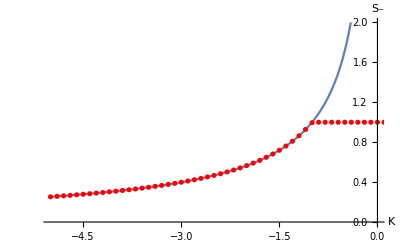

```mathematica
p1=Plot[1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2)/.k->k1,{k1,-5,0},AxesLabel->{"K","S_-"},LabelStyle->15,PlotRange->{0,2}];
p2=ListPlot[dataReal[[All,{1,3}]],PlotStyle->{Red}];
Show[{p1,p2}]
```

```mathematica
TrigExpand[Cos[2a]]
```

Cos[a]^2-Sin[a]^2

```mathematica
Clear[s,k];
ssol=Solve[k^2 s^3+k^2 s^2-2==0,s]//TableForm
```

s→1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2)
s→-1/3-((1+ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1-ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)
s→-1/3-((1-ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1+ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)

```mathematica
1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2)//TeXForm
```

\frac{1}{3} \left(\frac{k^2}{\sqrt[3]{-k^6+27 k^4+3 \sqrt{3} \sqrt{27 k^8-2 k^{10}}}}+\frac{\sqrt[3]{-k^6+27 k^4+3 \sqrt{3} \sqrt{27 k^8-2 k^{10}}}}{k^2}-1\right)

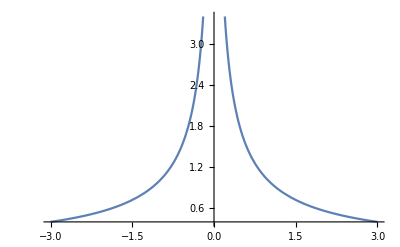

```mathematica
Plot[s/.ssol/.k->k1,{k1,-3,3}]
```

#### My ansatz

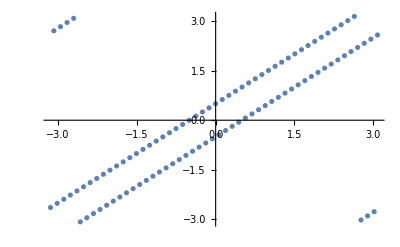

{0,0.877583}

```mathematica
mod[x_]:=Mod[x,2π]-π;
{A,n}={0.5,100};
α=Table[(2π i)/n,{i,0,n-1}];
data=Table[{α[[i]],α[[i]]+(-1)^(i-1)A}//mod,{i,1,n}];
ListPlot[data]
{x,θ}={data[[All,1]],data[[All,2]]};
{sp1,sm1}={N[Total[Exp[ⅈ(x+θ)]]/Length[x]],N[Total[Exp[ⅈ(x-θ)]]/Length[x]]}//Chop
```

### Solve cubic myself

```mathematica
temp1=k^2 s^3+k^2 s^2-2+2 e^2;
ssol=Solve[temp1==0,s];
Manipulate[Plot[s/.ssol[[1]]/.e->e1,{k,-10,10},PlotRange->{0,1},AxesLabel->{"K","S_-"},LabelStyle->15],{e1,0,2}]
```

```mathematica
ssol[[1]]/.{k->K,e->Ε}
```

{s→-1/3+(2^(1/3) K^2)/(3 (54 K^4-2 K^6-54 K^4 Ε^2+√(-4 K^12+(54 K^4-2 K^6-54 K^4 Ε^2)^2))^(1/3))+((54 K^4-2 K^6-54 K^4 Ε^2+√(-4 K^12+(54 K^4-2 K^6-54 K^4 Ε^2)^2))^(1/3))/(3 2^(1/3) K^2)}

```mathematica
TeXForm[-1/3+(2^(1/3) K^2)/(3 (54 K^4-2 K^6-54 K^4 Ε^2+√(-4 K^12+(54 K^4-2 K^6-54 K^4 Ε^2)^2))^(1/3))+((54 K^4-2 K^6-54 K^4 Ε^2+√(-4 K^12+(54 K^4-2 K^6-54 K^4 Ε^2)^2))^(1/3))/(3 2^(1/3) K^2)]
```

\frac{\sqrt[3]{2} K^2}{3 \sqrt[3]{-54 E^2 K^4+\sqrt{\left(-54 E^2 K^4-2 K^6+54 K^4\right)^2-4 K^{12}}-2 K^6+54 K^4}}+\frac{\sqrt[3]{-54 E^2 K^4+\sqrt{\left(-54 E^2 K^4-2 K^6+54 K^4\right)^2-4 K^{12}}-2
   K^6+54 K^4}}{3 \sqrt[3]{2} K^2}-\frac{1}{3}

```mathematica
FullSimplify[ssol[[1]]]
```

{s→-1/3+(k^4+(-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(2/3))/(3 k^2 (-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(1/3))}

```mathematica
TeXForm[(-1+e^2) k^8 (-27+27 e^2+2 k^2)]/.k->K
```

\left(e^2-1\right) K^8 \left(27 e^2+2 K^2-27\right)

```mathematica
Manipulate[Plot[-1/3+(k^4+(-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(2/3))/(3 k^2 (-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(1/3))/.k->k1,{e,0,2}],{k1,-10,0}]
```

```mathematica
Solve[-1/3+(k^4+(-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(2/3))/(3 k^2 (-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(1/3))==1,e]
```

{{e→-√(1-k^2)},{e→√(1-k^2)}}

```mathematica
Solve[-1/3+(k^4+(-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(2/3))/(3 k^2 (-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(1/3))==0,e]
```

{{e→-1},{e→1}}

## Bursty async

### Make data

#### (k, E) = (-0.1, 1.1)

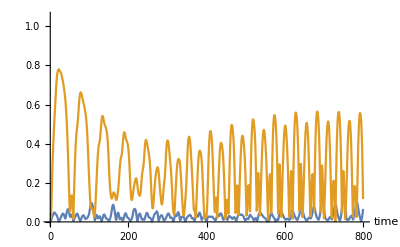

```mathematica
(*Preamble*)
{dt,n,T}={0.25,300,200}; 
{J,k}={-0.1,-0.1};
{e,b}={1.1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*Main sim*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wpa,Wma}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wpa,Abs[Wp1]];AppendTo[Wma,Abs[Wm1]];
]

ListPlot[{Abs[Wpa],Abs[Wma]},Joined->True,AxesLabel->{"time"},LabelStyle->15,PlotRange->{0,1.05},PlotRange->All]
```

#### (k, E) = (-0.1, 1.1)

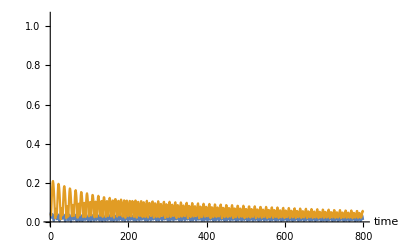

```mathematica
(*Preamble*)
{dt,n,T}={0.25,300,200}; 
{J,k}={-0.1,-0.1};
{e,b}={2,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*Main sim*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wpb,Wmb}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wpb,Abs[Wp1]];AppendTo[Wmb,Abs[Wm1]];
]

ListPlot[{Abs[Wpb],Abs[Wmb]},Joined->True,AxesLabel->{"time"},LabelStyle->15,PlotRange->{0,1.05},PlotRange->All]
```

#### (k, E) = (-1.5, 1.1)

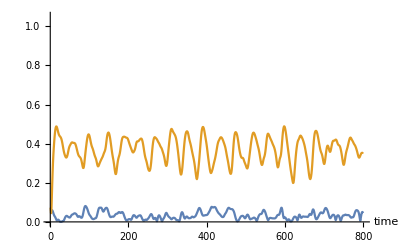

```mathematica
(*Preamble*)
{dt,n,T}={0.25,300,200}; 
{J,k}={-1.5,-1.5};
{e,b}={0.85,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*Main sim*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wp3,Wm3}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp3,Abs[Wp1]];AppendTo[Wm3,Abs[Wm1]];
]

ListPlot[{Abs[Wp3],Abs[Wm3]},Joined->True,AxesLabel->{"time"},LabelStyle->15,PlotRange->{0,1.05},PlotRange->All]
```

#### E = 3

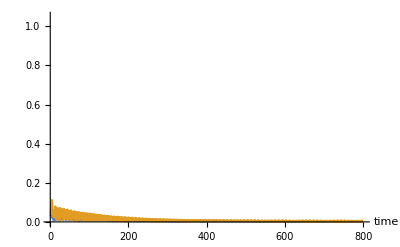

```mathematica
(*Preamble*)
{dt,n,T}={0.25,300,200}; 
{J,k}={-1.5,-1.5};
{e,b}={3,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*Main sim*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wp4,Wm4}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp4,Abs[Wp1]];AppendTo[Wm4,Abs[Wm1]];
]

ListPlot[{Abs[Wp4],Abs[Wm4]},Joined->True,AxesLabel->{"time"},LabelStyle->15,PlotRange->{0,1.05},PlotRange->All]
```

### Make plot

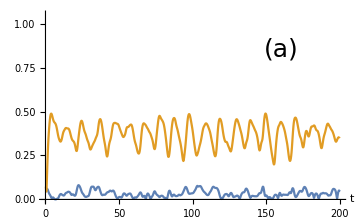
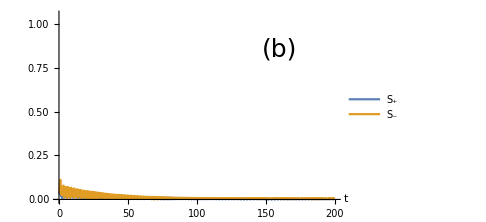
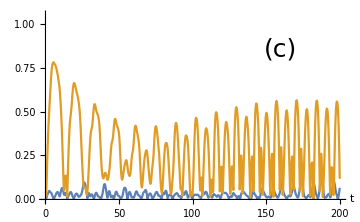
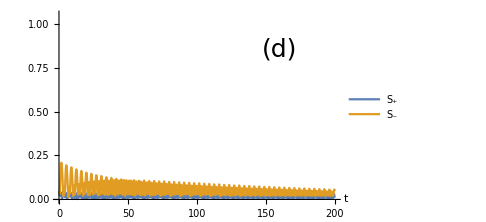
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
ts=Table[dt*i,{i,1,Length[Wp3]}];
p1=ListPlot[{{ts,Abs[Wp3]}ᵀ,{ts,Abs[Wm3]}ᵀ},Joined->True,AxesLabel->{Style["t",30,Italic]},LabelStyle->20,PlotRange->{0,1.05},PlotRange->All,ImageSize->Medium,Epilog->{Text[Style["(a)",25],{160,0.85}]}];
p2=ListPlot[{{ts,Abs[Wp4]}ᵀ,{ts,Abs[Wm4]}ᵀ},Joined->True,AxesLabel->{Style["t",30,Italic]},LabelStyle->20,PlotRange->{0,1.05},PlotRange->All,ImageSize->Medium,PlotLegends->{Style["S_+",30],Style["S_-",30]},
Epilog->{Text[Style["(b)",25],{160,0.85}]}];
ts=Table[dt*i,{i,1,Length[Wpa]}];
p3=ListPlot[{{ts,Abs[Wpa]}ᵀ,{ts,Abs[Wma]}ᵀ},Joined->True,AxesLabel->{Style["t",30,Italic]},LabelStyle->20,PlotRange->{0,1.05},PlotRange->All,ImageSize->Medium,
Epilog->{Text[Style["(c)",25],{160,0.85}]}];
p4=ListPlot[{{ts,Abs[Wpb]}ᵀ,{ts,Abs[Wmb]}ᵀ},Joined->True,AxesLabel->{Style["t",30,Italic]},LabelStyle->20,PlotRange->{0,1.05},PlotRange->All,ImageSize->Medium,PlotLegends->{Style["S_+",30],Style["S_-",30]},
Epilog->{Text[Style["(d)",25],{160,0.85}]}];
ptog=Grid[{{p1,p2},{p3,p4}}]
SetDirectory[NotebookDirectory[]];
Export["figures/busty-async.png",ptog];
```

## Bif diagram (K,E) space

### Develop

```mathematica
findVmean[xs_,thetas_,dt_]:=Module[{vx,vtheta,tcutoff,vxMean,vthetaMean,vMean,n,T,index},
{vx,vtheta}={{},{}};
{T,n}=Dimensions[xs];
tcutoff=Round[0.9T];
vxMean=Table[Mean[Differences[xs[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vthetaMean=Table[Mean[Differences[thetas[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vMean=√(vxMean^2+vthetaMean^2);
Return[vMean]
];

run[k1_,e_]:=Module[{J,K,dt,n,T,k,b,Ex,Eθ,b1,b2,t,NT,pin,z00,z0,znew,Wp,Wm,Wp1,Wm1,xs,x,theta,thetas,vmean,Sp,Sm,cutoff},

{dt,n,T}={0.5,100,100}; 
{J,k,b}={k1,k1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
{xs,thetas}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp1,Wm1}=findWs[znew];
{x,theta}=znew;AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
AppendTo[xs,x];AppendTo[thetas,theta];
];

cutoff=Round[0.9Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
vmean=findVmean[xs,thetas];
Return[{vmean,Sp,Sm}]
]
```

### Make data

```mathematica
data=Flatten[ParallelTable[{k,e,run[k,e]},{k,-5,5,0.05},{e,0,1.5,0.05}],1];
data={data[[All,1]],data[[All,2]],data[[All,3]]/Max[data[[All,3]]]}ᵀ;
```

$Aborted

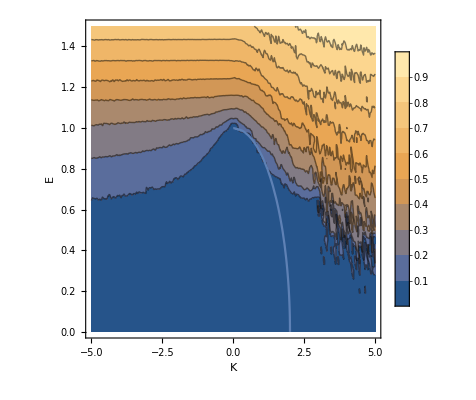

```mathematica
p1=ListContourPlot[data//Chop,FrameLabel->{Style["K",17,Italic],Style["E",Italic,17]},PlotLegends->Automatic,LabelStyle->13];
p2=ContourPlot[√(1-e1^2)-k/2==0,{k,-5,5},{e1,0,2}];
Show[{p1,p2}]
```

### Data here

```mathematica
{dt,n,T}={0.5,100,100}; 
{J,k,b}={k1,k1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
{xs,thetas}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp1,Wm1}=findWs[znew];
{x,theta}=znew;AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
AppendTo[xs,x];AppendTo[thetas,theta];
];

cutoff=Round[0.9Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
vmean=findVmean[xs,thetas];
```

```mathematica
data=Flatten[ParallelTable[{k,e,run[k,e]}//Flatten,{k,-3,3,1},{e,0,1.2,0.5}],1];
```

```mathematica
data=Flatten[ParallelTable[{k,e,run[k,e]}//Flatten,{k,-3,3,0.025},{e,0,1.2,0.025}],1];
(*data=Flatten[ParallelTable[{k,e,run[k,e]}//Flatten,{k,-3,3,1},{e,0,1.2,0.5}],1];*)
data={data[[All,1]],data[[All,2]],data[[All,3]]/Max[data[[All,3]]],data[[All,4]],data[[All,5]]}ᵀ;
```

$Aborted

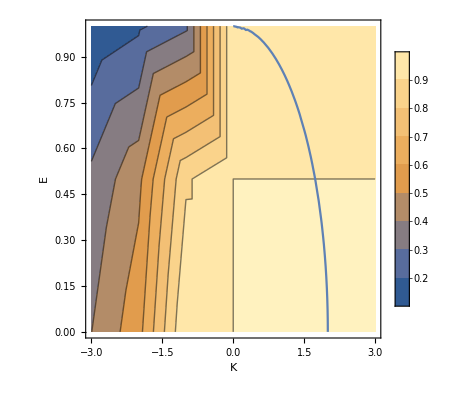

```mathematica
p1=ListContourPlot[data[[All,{1,2,4}]],FrameLabel->{Style["K",17,Italic],Style["E",Italic,17]},PlotLegends->Automatic,LabelStyle->13];
p2=ContourPlot[√(1-e1^2)-k/2==0,{k,-5,5},{e1,0,2}];
Show[{p1,p2}]
```

#### First

```mathematica
vmeans=Chop[data[[All,3]]];
sps=data[[All,4]];
sms=data[[All,5]];
temp=Table[
condSync=sms[[i]]>0.5&&vmeans[[i]]<0.01;
condPinned=sps[[i]]>0.95&&sms[[i]]<0.5&&vmeans[[i]]<0.01;
condFlipped=sps[[i]]<0.99&&vmeans[[i]]<0.01;
condUnsteady=vmeans[[i]]>0.01;
Which[condPinned,"pinned",condSync,"sync",condFlipped,"flipped",condUnsteady,"unsteady"],
{i,1,Length[sms]}
];
temp;
```

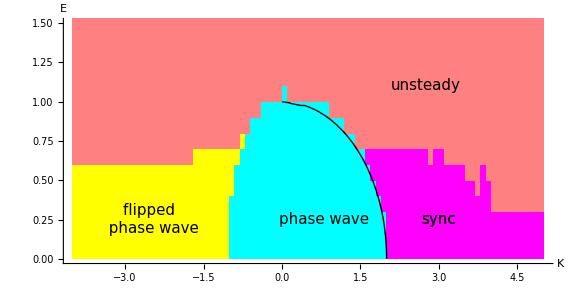

figures/bif-diagram-E-non-zero.png

```mathematica
Clear[colmap];
colmap[x1_]:=Which[x1=="pinned",Cyan,x1=="sync",Magenta,x1=="flipped",Yellow,x1=="unsteady",Pink,True,Cyan];
SetAttributes[colmap,Listable];
alldata={data[[All,1]],data[[All,2]],temp//colmap}ᵀ;
p1=Graphics[Table[{alldata[[i,3]],Rectangle[{alldata[[i,1]],alldata[[i,2]]}]},{i,1,Length[alldata]}],
AspectRatio->0.5,Axes->True,PlotRange->{0,1.5},LabelStyle->15,AxesLabel->{Style["K",18,Italic],Style["E",18,Italic]},
Epilog->{Text[Style["unsteady",15],{2.75,1.1}],Text[Style["sync",15],{3,0.25}],Text[Style["sync",15],{3,0.25}],
Text[Style["phase wave",15],{0.8,0.25}],Text[Style["flipped \n phase wave",15],{-2.5,0.25}]
},ImageSize->Large];
p2=ContourPlot[√(1-e1^2)-k/2==0,{k,-5,5},{e1,0,1.3},ContourStyle->{Thick,Black}];
pc=Show[{p1,p2}]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-E-non-zero.png",pc]
```

### Finer grain

```mathematica
run1[k1_,e_,T_,n_]:=Module[{J,K,dt,k,b,Ex,Eθ,b1,b2,t,NT,pin,z00,z0,znew,Wp,Wm,Wp1,Wm1,xs,x,theta,thetas,vmean,Sp,Sm,cutoff},

{dt}={0.5}; 
{J,k,b}={k1,k1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
{xs,thetas}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp1,Wm1}=findWs[znew];
{x,theta}=znew;AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
AppendTo[xs,x];AppendTo[thetas,theta];
];

cutoff=Round[0.9Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
vmean=findVmean[xs,thetas,dt];
Return[{vmean,Sp,Sm}]
]
```

```mathematica
data=Flatten[ParallelTable[{k,e,run1[k,e,150,200]}//Flatten,{k,-3,3,0.025},{e,0,1.2,0.025}],1];
data={data[[All,1]],data[[All,2]],data[[All,3]]/Max[data[[All,3]]],data[[All,4]],data[[All,5]]}ᵀ;
SetDirectory[NotebookDirectory[]];
Export["data/bif-diagram-e-non-zero.csv",data];
```

```mathematica
vmeans=Chop[data[[All,3]]];
sps=data[[All,4]];
sms=data[[All,5]];
temp=Table[
condSync=sms[[i]]>0.5&&vmeans[[i]]<0.01;
condPinned=sps[[i]]>0.95&&sms[[i]]<0.5&&vmeans[[i]]<0.01;
condFlipped=sps[[i]]<0.99&&vmeans[[i]]<0.01;
condUnsteady=vmeans[[i]]>0.01;
Which[condPinned,"pinned",condSync,"sync",condFlipped,"flipped",condUnsteady,"unsteady"],
{i,1,Length[sms]}
];
Clear[colmap];
colmap[x1_]:=Which[x1=="pinned",Cyan,x1=="sync",Magenta,x1=="flipped",Yellow,x1=="unsteady",Pink,True,Cyan];
SetAttributes[colmap,Listable];
alldata={data[[All,1]],data[[All,2]],temp//colmap}ᵀ;
```

#### Load data

```mathematica
data=Import["data/bif-diagram-e-non-zero.csv"];
vmeans=Chop[data[[All,3]]];
sps=data[[All,4]];
sms=data[[All,5]];
temp=Table[
condSync=sms[[i]]>0.5&&vmeans[[i]]<0.01;
condPinned=sps[[i]]>0.95&&sms[[i]]<0.5&&vmeans[[i]]<0.01;
condFlipped=sps[[i]]<0.99&&vmeans[[i]]<0.01;
condUnsteady=vmeans[[i]]>0.01;
Which[condPinned,"pinned",condSync,"sync",condFlipped,"flipped",condUnsteady,"unsteady"],
{i,1,Length[sms]}
];
Clear[colmap];
colmap[x1_]:=Which[x1=="pinned",Cyan,x1=="sync",Magenta,x1=="flipped",Yellow,x1=="unsteady",Pink,True,Cyan];
SetAttributes[colmap,Listable];
alldata={data[[All,1]],data[[All,2]],temp//colmap}ᵀ;
```

#### Plot

```mathematica
p1=Graphics[Table[{alldata[[i,3]],Rectangle[{alldata[[i,1]],alldata[[i,2]]}]},{i,1,Length[alldata]}],
AspectRatio->0.5,Axes->True,PlotRange->{0,1.21},LabelStyle->15,AxesLabel->{Style["K",18,Italic],Style["E",18,Italic]},
Epilog->{
Text[Style["sync",15],{3,0.4}],
Text[Style["phase wave",15],{0.8,0.4}],
Text[Style["split \n phase wave",15],{-2.0,0.25}],
Text[Style["bursty async",15],{-1.8,0.99}],
Rotate[Text[Style["hysteresis",13],{0.8,0.75}],-01 Degree],
Text[Style["quasi \n periodicity",14],{1.6,0.95}],
Text[Style["chaos",15],{1.05,1.15}],
Text[Style["periodic (flying saucers)",15],{2.85,1.2}]
},ImageSize->Large];
p2=ContourPlot[{√(1-e1^2)-k/2==0,√(1-e1^2)+k==0},{k,-5,5},{e1,0,1.3},ContourStyle->{{Thick,Black},{Thick,Black}}];
pc=Show[{p1,p2}]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-E-non-zero.png",pc]
```

-Graphics-

figures/bif-diagram-E-non-zero.png

```mathematica
p1=Graphics[Table[{alldata[[i,3]],Rectangle[{alldata[[i,1]],alldata[[i,2]]}]},{i,1,Length[alldata]}],
AspectRatio->0.5,Axes->True,PlotRange->{0,1.18},LabelStyle->15,AxesLabel->{Style["K",18,Italic],Style["E",18,Italic]},
Epilog->{
Text[Style["sync",15],{3,0.4}],
Text[Style["phase wave",15],{0.8,0.4}],
Text[Style["split \n phase wave",15],{-2.0,0.25}],
Text[Style["Unsteady",15],{-1.8,0.99}],
Text[Style["Unsteady",15],{2.2,0.99}],
},ImageSize->Large];
p2=ContourPlot[{√(1-e1^2)-k/2==0,√(1-e1^2)+k==0},{k,-5,5},{e1,0,1.3},ContourStyle->{{Thick,Black},{Thick,Black}}];
pc=Show[{p1,p2}]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-E-non-zero.png",pc]
```

-Graphics-

figures/bif-diagram-E-non-zero.png

### Finer grain: N = 200

```mathematica
run1[k1_,e_,T_,n_]:=Module[{J,K,dt,k,b,Ex,Eθ,b1,b2,t,NT,pin,z00,z0,znew,Wp,Wm,Wp1,Wm1,xs,x,theta,thetas,vmean,Sp,Sm,cutoff},

{dt}={0.5}; 
{J,k,b}={k1,k1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
{xs,thetas}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp1,Wm1}=findWs[znew];
{x,theta}=znew;AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
AppendTo[xs,x];AppendTo[thetas,theta];
];

cutoff=Round[0.9Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
vmean=findVmean[xs,thetas];
Return[{vmean,Sp,Sm}]
]
```

```mathematica
data=Flatten[ParallelTable[{k,e,run1[k,e,150,200]}//Flatten,{k,-3,3,0.025},{e,0,1.2,0.025}],1];
data={data[[All,1]],data[[All,2]],data[[All,3]]/Max[data[[All,3]]],data[[All,4]],data[[All,5]]}ᵀ;
```

```mathematica
vmeans=Chop[data[[All,3]]];
sps=data[[All,4]];
sms=data[[All,5]];
temp=Table[
condSync=sms[[i]]>0.5&&vmeans[[i]]<0.01;
condPinned=sps[[i]]>0.95&&sms[[i]]<0.5&&vmeans[[i]]<0.01;
condFlipped=sps[[i]]<0.99&&vmeans[[i]]<0.01;
condUnsteady=vmeans[[i]]>0.01;
Which[condPinned,"pinned",condSync,"sync",condFlipped,"flipped",condUnsteady,"unsteady"],
{i,1,Length[sms]}
];
temp;
```

```mathematica
Clear[colmap];
colmap[x1_]:=Which[x1=="pinned",Cyan,x1=="sync",Magenta,x1=="flipped",Yellow,x1=="unsteady",Pink,True,Cyan];
SetAttributes[colmap,Listable];
alldata={data[[All,1]],data[[All,2]],temp//colmap}ᵀ;
p1=Graphics[Table[{alldata[[i,3]],Rectangle[{alldata[[i,1]],alldata[[i,2]]}]},{i,1,Length[alldata]}],
AspectRatio->0.5,Axes->True,PlotRange->{0,1.5},LabelStyle->15,AxesLabel->{Style["K",18,Italic],Style["E",18,Italic]},
Epilog->{
Text[Style["unsteady",15],{2.75,1.0}],
Text[Style["sync",15],{3,0.4}],
Text[Style["phase wave",15],{0.8,0.4}],
Text[Style["flipped \n phase wave",15],{-2.0,0.25}]
},ImageSize->Large];
p2=ContourPlot[{√(1-e1^2)-k/2==0,√(1-e1^2)+k==0},{k,-5,5},{e1,0,1.3},ContourStyle->{{Thick,Black},{Thick,Black}}];
pc=Show[{p1,p2}]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-E-non-zero.png",pc]
```

-Graphics-

figures/bif-diagram-E-non-zero.png

## E = 0 limit -- pictures

### Warm up

```mathematica
(*Preamble*)
{dt,n,T}={0.1,200,400}; 
{J,k}={-10,-10};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]
results=plotResults[znew,pin]
```

```mathematica
size=25;
```

### Pinned state

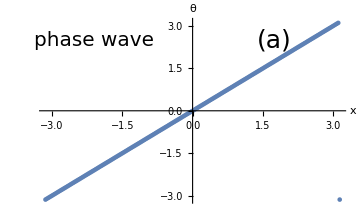

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={1,1};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p1=ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["phase wave",20],{-2.1,2.5}],Text[Style["(a)",25],{1.75,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

### Sync state

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={2,2};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;
```

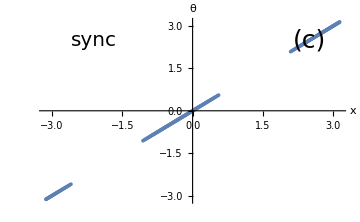

```mathematica
{x,θ}=znew;
p2= ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["sync",20],{-2.1,2.5}],Text[Style["(c)",25],{2.5,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

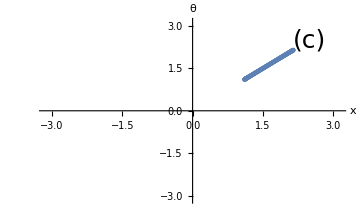

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={3,3};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{-0.25π,-0.5π}],{i,1,2},{j,1,n}],Table[RandomReal[{0.5π,1.0π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p4= ListPlot[{Mod[x,2π]-1.2π,Mod[θ,2π]-1.2π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,LabelStyle->15,ImageSize->Medium,PlotRange->{{-π,π},{-π,π}},
Epilog->{Text[Style["sync",20],{-2.1,2.5}],Text[Style["(c)",25],{2.5,2.5}]}]
```

### Split phase wave

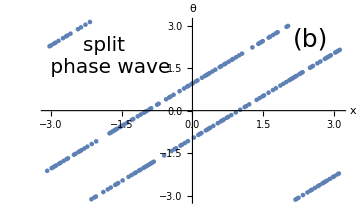

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={-2,-2};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p3= ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["split \n phase wave",20],{-1.8,1.9}],Text[Style["(b)",25],{2.5,2.5}]}]
```

### Plot together

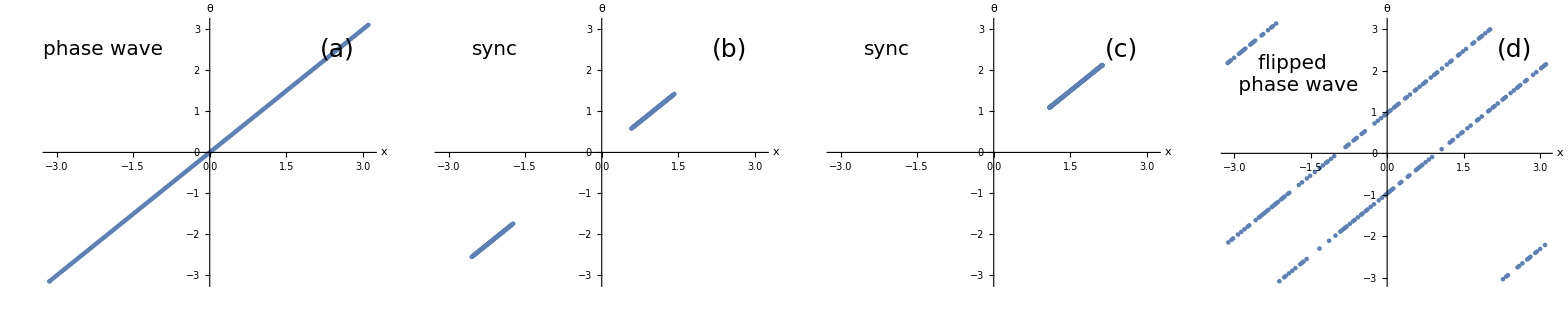

```mathematica
pAll=Grid[{{p1,p2,p4,p3}}]
SetDirectory[NotebookDirectory[]];
Export["figures/states-undriven.png",pAll];
```

```mathematica
pAll=Grid[{{p1,SpanFromLeft},{p3,p2}},Alignment->{Center,Center}]
SetDirectory[NotebookDirectory[]];
Export["figures/states-undriven.png",pAll];
```

-Graphics- | 
-Graphics- | -Graphics-

```mathematica
Clear[sm,k];
```

```mathematica
sol=Solve[sm==-2/k √((1-sm)/2) 1/(√(1-sm^2)) ,sm]//TableForm
```

sm→1/3 (-1+1/((-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3))+(-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3))
sm→-1/3-(1+ⅈ √3)/(6 (-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3))-1/6 (1-ⅈ √3) (-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3)
sm→-1/3-(1-ⅈ √3)/(6 (-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3))-1/6 (1+ⅈ √3) (-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3)

```mathematica
temp=sm-(-2/k √((1-sm)/2) 1/(√(1-sm^2)) );
FullSimplify[temp]
```

sm+(√2)/(k √(1+sm))

```mathematica
Numerator[Together[Numerator[temp]]]
```

√2 √(1-sm)+k sm √(1-sm^2)

```mathematica
sol=Solve[k^2 S^4-k^2 S^2-2S+2==0,S]//Flatten;
TableForm[sol]
```

S→1
S→1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2)
S→-1/3-((1+ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1-ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)
S→-1/3-((1-ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1+ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)

```mathematica
sol
```

{{S→1},{S→1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2)},{S→-1/3-((1+ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1-ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)},{S→-1/3-((1-ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1+ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)}}

```mathematica
sol
```

{S→1,S→1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2),S→-1/3-((1+ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1-ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2),S→-1/3-((1-ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1+ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)}

```mathematica
FullSimplify[1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2),Assumptions->{k∈Reals}]
```

1/3 (-1+k^2/((27 k^4-k^6+3 √(81 k^8-6 k^10))^(1/3))+((27 k^4-k^6+3 √(81 k^8-6 k^10))^(1/3))/k^2)

```mathematica
(-1+k^2/((27 k^4-k^6+3 √(81 k^8-6 k^10))^(1/3))+((27 k^4-k^6+3 √(81 k^8-6 k^10))^(1/3))/k^2)/.k->K//TeXForm
```

\frac{K^2}{\sqrt[3]{-K^6+27 K^4+3 \sqrt{81 K^8-6 K^{10}}}}+\frac{\sqrt[3]{-K^6+27 K^4+3 \sqrt{81 K^8-6 K^{10}}}}{K^2}-1

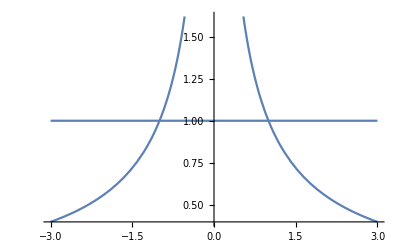

```mathematica
Plot[{S/.sol[[{1}]],S/.sol[[2]]}/.k->k1,{k1,-3,3}]
```

```mathematica
temp=sm+(2/k √((1-sm)/(2(1-sm)^2)));
```

```mathematica
t1=Numerator[Together[temp]]^2
```

(√2 √(-1/(-1+sm))+k sm)^2

```mathematica
Expand[t1^2]
```

4/(-1+sm)^2-(8 √2 k √(-1/(-1+sm)) sm)/(-1+sm)-(12 k^2 sm^2)/(-1+sm)+4 √2 k^3 √(-1/(-1+sm)) sm^3+k^4 sm^4

## S(K) when E = 0

### S(K)

#### S+(K) in sync state data

This was computed in another notebook. It is the numerical solution to the integral equation for S_+.

```mathematica
splusdata={{1.999993743562679,0.005000015641142232},{1.9999234335111766,0.017500669982426307},{1.9997749494458865,0.030003376138212596},{1.999548233472551,0.042509602207686306},{1.999243177285357,0.05502082050336764},{1.9988596372556655,0.0675385091998497},{1.9983974322939322,0.08006415411389829},{1.9978563434718877,0.0925992504939098},{1.9972361135730605,0.10514530484045247},{1.996536446487564,0.11770383676863361},{1.9957570065381822,0.13027638091622842},{1.9948974177367746,0.14286448890356204},{1.9939572628668112,0.15546973135938616},{1.9929360825510611,0.16809370001027968},{1.9918333741641183,0.18073800985038505},{1.9906485906204932,0.19340430139907017},{1.9893811390586922,0.2060942430538968},{1.9880303793895913,0.21880953355127472},{1.9865956226907415,0.23155190454761693},{1.9850761294765196,0.24432312332922898},{1.9834711077837286,0.25712499566976754},{1.9817797110929343,0.26995936884677885},{1.9800010360816769,0.282828134831794},{1.9781341201359923,0.29573323367971777},{1.9761779386820664,0.3086766571267442},{1.974131401925707,0.3216604524808108},{1.9719933533455132,0.3346867264437284},{1.9697625628866329,0.34775765003684084},{1.9674377265293466,0.3608754627535145},{1.965017460499127,0.3740424778786982},{1.962500297136882,0.38726108786264885},{1.9598846802719936,0.4005337701252187},{1.9571689587642596,0.41386309361427226},{1.9543513824740824,0.4272517252977019},{1.951430094354156,0.44070243791368074},{1.948403062911361,0.45421813219571094},{1.9452683772110595,0.4678017751487185},{1.9420236400147648,0.4814565491040531},{1.938666545569754,0.4951857255667795},{1.9351945858481454,0.5089927427470043},{1.9316400055646434,0.5228717551357426},{1.9286435559735016,0.5366465964093475},{1.926761081768007,0.5501460508156717},{1.9261599289947064,0.5632969431392331},{1.9268805255618302,0.5760606250750041},{1.928903641644791,0.5884171585845404},{1.9321798364930005,0.6003581954904653},{1.9366448108369938,0.6118829810035521},{1.942227978247196,0.6229958653422291},{1.9488573857755704,0.6337046563869101},{1.9564625362191885,0.6440194875568208},{1.9649759618576907,0.6539520202502421},{1.9743340431977334,0.6635148720214822},{1.9844773633892576,0.6727212033902841},{1.9953507828613777,0.681584416976412},{2.006903345793346,0.6901179386157718},{2.019088090216493,0.6983350586991054},{2.0318618069490175,0.7062488182475126},{2.045184775864993,0.7138719284581536},{2.0590204973246893,0.7212167153894183},{2.0733354291631,0.7282950837383362},{2.0880987366855193,0.7351184946534354},{2.1032820574211804,0.7416979546303476},{2.11885928354008,0.7480440123196209},{2.13480636167157,0.7541667614009526},{2.151101109868663,0.7600758478990438},{2.167723050912724,0.7657804807219504},{2.184653260918433,0.7712894444821968},{2.2018742320911335,0.7766111138763818},{2.2193697484619506,0.7817534690658794},{2.237124773449978,0.7867241116309382},{2.25512534815476,0.7915302807715594},{2.273358499392864,0.796178869493477},{2.2918121562745415,0.800676440683029},{2.3104750751412144,0.8050292426921403},{2.3293367710834967,0.8092432246811547},{2.348387456136924,0.8133240513649865},{2.3676179831557462,0.8172771172403743},{2.387019794853274,0.8211075602414413},{2.406584877490138,0.8248202748079188},{2.4263057187456503,0.8284199243610263},{2.4461752693560403,0.8319109531900853},{2.466186908147007,0.8352975977590432},{2.4863344101271725,0.8385838974465837},{2.5066119173440278,0.8417737047367605},{2.527013912235224,0.8448706948793652},{2.547535193235947,0.8478783750407416},{2.5681708524279965,0.8508000929666563},{2.5889162550383102,0.8536390451792707},{2.6097670206144867,0.8563982847303171},{2.630719005722392,0.8590807285323896},{2.651768288026675,0.8616891642898366},{2.672911151628988,0.8642262570501761},{2.694144073551201,0.8666945553962857},{2.7154637112620446,0.8690964972988563},{2.7368668911555782,0.8714344156478085},{2.7583505978987777,0.8737105434805336},{2.7799119645735146,0.8759270189239844},{2.801548263545343,0.8780858898667981},{2.8232568979978487,0.8801891183768176},{2.845035394077151,0.8822385848785436},{2.8668813935961928,0.884236092104289},{2.88879264725315,0.8861833688320301},{2.9107670083224453,0.8880820734222219},{2.9328024267805586,0.889933797165152},{2.954896943832269,0.8917400674497321},{2.9770486868059365,0.8935023507640039},{2.9992558643892533,0.8952220555370152},{3.0215167621793255,0.8969005348311743},{3.0438297385232103,0.8985390888936343},{3.0661932206270945,0.9001389675747579},{3.088605700914084,0.9017013726212327},{3.111065733612339,0.9032274598509465},{3.133571931556683,0.9047183412163239},{3.1561229631883236,0.9061750867624038},{3.1787175497384768,0.9075987264855766},{3.201354462582891,0.9089902520985357},{3.224032520755264,0.9103506187066744},{3.2467505886085313,0.9116807464008405},{3.2695075736138266,0.9129815217710711},{3.292302424287768,0.9142537993456523},{3.31513412823936,0.9154984029595981},{3.338001710328556,0.916716127056388},{3.360904230929051,0.9179077379265907},{3.3838407842884664,0.919073974886778},{3.40681049697962,0.9202155514019328},{3.429812526436966,0.9213331561543787},{3.452846059572806,0.9224274540620698},{3.4759103114681955,0.9234990872489214},{3.499004524133881,0.9245486759697065},{3.5221279653368884,0.9255768194918996},{3.5452799274887523,0.926584096936705},{3.568459726591586,0.9275710680813929},{3.5916667012385153,0.9285382741249303},{3.6149002116652036,0.9294862384187941},{3.6381596388494257,0.9304154671647406},{3.661444383655866,0.9313264500812074},{3.684753866023476,0.9322196610399341},{3.708087524192955,0.9330955586742905},{3.7314448139720002,0.9339545869607339},{3.754825208036228,0.9347971757747201},{3.7782281952636985,0.9356237414223385},{3.801653280101183,0.9364346871488608},{3.825099981960403,0.93723040362533},{3.8485678346426018,0.9380112694142586},{3.8720563857898536,0.9387776514154492},{3.895565196361714,0.9395299052928878},{3.9190938401358153,0.940268375883617},{3.94264190323111,0.9409933975894533},{3.966208983652612,0.9417052947523472},{3.9897946908564506,0.9424043820141704},{4.013398645334218,0.9430909646616461},{4.037020478215578,0.9437653389571274},{4.060659830888234,0.9444277924558675},{4.084316354634311,0.9450786043104137},{4.1079897102824,0.945718045562709},{4.1316795678744125,0.9463463794244655},{4.155385606346528,0.9469638615463404},{4.179107513223551,0.9475707402764203},{4.202844984325986,0.9481672569084936},{4.22659772348925,0.9487536459205659},{4.250365442294405,0.9493301352040548},{4.274147859809853,0.9498969462840744},{4.2979447023435,0.9504542945311981},{4.321755703204866,0.9510023893650805},{4.345580602476684,0.9515414344502837},{4.369419146795546,0.9520716278846496},{4.393271089141154,0.9525931623805448},{4.417136188633822,0.9531062254392718},{4.441014210339811,0.9536109995189466},{4.464904925084169,0.9541076621961189},{4.488808109270702,0.9545963863213968},{4.51272354470881,0.9550773401693285},{4.536651018446835,0.9555506875827806},{4.560590322611633,0.9560165881120475},{4.584541254254154,0.9564751971488973},{4.608503615200692,0.9569266660557774},{4.632477211909605,0.9573711422903677},{4.656461855333255,0.9578087695256771},{4.680457360784961,0.9582396877658589},{4.704463547810716,0.9586640334579241},{4.728480240065514,0.9590819395995117},{4.752507265194043,0.9594935358428779},{4.776544454715612,0.959898948595252},{4.800591643913101,0.9602983011157045},{4.824648671725769,0.960691713608665},{4.848715380645792,0.9610793033142196},{4.87279161661835,0.9614611845953153},{4.896877228945129,0.9618374690219902},{4.920972070191107,0.9622082654527474},{4.94507599609447,0.9625736801131793},{4.9691888654795875,0.9629338166719469},{4.9933105401728355,0.9632887763142228},{5.017440884921268,0.9636386578126811},{5.041579767313925,0.963983557596141},{5.065727057705745,0.96432356981594},{5.089882629143931,0.9646587864101333},{5.114046357296724,0.9649892971655883},{5.138218120384448,0.9653151897780645},{5.1623977991127745,0.9656365499103423},{5.186585276608102,0.9659534612484806},{5.210780438354977,0.9662660055562684},{5.23498317213549,0.9665742627279345},{5.259193367970557,0.9668783108391829},{5.283410918063032,0.96717822619661},{5.307635716742572,0.967474083385565},{5.331867660412201,0.9677659553165076},{5.356106647496509,0.9680539132699161},{5.380352578391407,0.9683380269398012},{5.404605355415426,0.9686183644758679},{5.428864882762467,0.9688949925243797},{5.453131066455954,0.9691679762677672},{5.477403814304366,0.9694373794630262},{5.501683035858076,0.9697032644789448},{5.5259686423674585,0.9699656923322054},{5.550260546742217,0.9702247227223939},{5.5745586635119135,0.9704804140659571},{5.5988629087876145,0.9707328235291462},{5.623173200224658,0.9709820070599768},{5.647489456986486,0.9712280194192376},{5.671811599709498,0.9714709142105895},{5.696139550468903,0.971710743909772},{5.720473232745546,0.9719475598929577},{5.744812571393642,0.972181412464278},{5.76915749260944,0.9724123508825482},{5.793507923900722,0.9726404233872201},{5.817863794057172,0.9728656772235862},{5.842225033121553,0.9730881586672584},{5.866591572361656,0.97330791304795},{5.890963344243035,0.9735249847725778},{5.915340282402471,0.9737394173477091},{5.939722321622137,0.9739512534013767},{5.964109397804482,0.9741605347042765},{5.988501447947763,0.974367302190375},{6.012898410122229,0.9745715959769383},{6.037300223446951,0.9747734553840061},{6.061706828067241,0.9749729189533247},{6.086118165132671,0.9751700244667596},{6.1105341767756665,0.9753648089642007},{6.134954806090641,0.9755573087609789}};
```

#### Make data

```mathematica
dataLower=ParallelTable[
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.25,500,200}; 
{J,k}={K,K};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

cutoff=Round[0.5 Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
{K,Sp,Sm},
{K,-5,5,0.1}
]
```

{{-5.,0.000481633,0.252708},{-4.9,0.000489747,0.257386},{-4.8,0.000498163,0.262269},{-4.7,0.000506835,0.267315},{-4.6,0.000515806,0.272561},{-4.5,0.000525092,0.278021},{-4.4,0.000534709,0.283708},{-4.3,0.000544676,0.289636},{-4.2,0.00055501,0.295822},{-4.1,0.000565733,0.302284},{-4.,0.000576865,0.309039},{-3.9,0.000588431,0.316109},{-3.8,0.000600454,0.323518},{-3.7,0.000612962,0.331289},{-3.6,0.000625982,0.339451},{-3.5,0.000639549,0.348035},{-3.4,0.000653694,0.357075},{-3.3,0.000668454,0.366609},{-3.2,0.000683869,0.376679},{-3.1,0.00069998,0.387332},{-3.,0.000716836,0.398623},{-2.9,0.000734483,0.410612},{-2.8,0.000752978,0.423365},{-2.7,0.000772379,0.436962},{-2.6,0.000792751,0.451491},{-2.5,0.000814186,0.467089},{-2.4,0.000836718,0.483798},{-2.3,0.000860452,0.501794},{-2.2,0.000885503,0.521285},{-2.1,0.000911924,0.542354},{-2.,0.000939849,0.565275},{-1.9,0.000969397,0.590312},{-1.8,0.0010007,0.617782},{-1.7,0.0010339,0.648072},{-1.6,0.00106915,0.681654},{-1.5,0.00110663,0.719119},{-1.4,0.00114652,0.76121},{-1.3,0.00118902,0.808898},{-1.2,0.00123434,0.86348},{-1.1,0.00128271,0.926779},{-1.,0.00133395,0.9976},{-0.9,0.00138017,1.},{-0.8,0.00142939,1.},{-0.7,0.00148225,1.},{-0.6,0.00153917,1.},{-0.5,0.00160064,1.},{-0.4,0.00166722,1.},{-0.3,0.00173958,1.},{-0.2,0.00181851,1.},{-0.1,0.00190494,1.},{0.,0.002,1.},{0.1,0.00210504,1.},{0.2,0.00222173,1.},{0.3,0.00235211,1.},{0.4,0.00249875,1.},{0.5,0.00266489,1.},{0.6,0.0028547,1.},{0.7,0.00307361,1.},{0.8,0.0033289,1.},{0.9,0.00363042,1.},{1.,0.00399202,1.},{1.1,0.00443361,1.},{1.2,0.00498505,1.},{1.3,0.00569316,1.},{1.4,0.00663574,1.},{1.5,0.00795239,1.},{1.6,0.00992094,1.},{1.7,0.0131851,1.},{1.8,0.0196529,1.},{1.9,0.038547,1.},{2.,0.314756,1.},{2.1,0.7397,1.},{2.2,0.775394,1.},{2.3,0.80203,1.},{2.4,0.823006,1.},{2.5,0.840094,1.},{2.6,0.854498,1.},{2.7,0.865693,1.},{2.8,0.875583,1.},{2.9,0.884379,1.},{3.,0.891761,1.},{3.1,0.895142,1.},{3.2,0.899505,1.},{3.3,0.902278,1.},{3.4,0.907822,1.},{3.5,0.91287,1.},{3.6,0.917798,1.},{3.7,0.92261,1.},{3.8,0.926837,1.},{3.9,0.929977,1.},{4.,0.933441,1.},{4.1,0.936359,1.},{4.2,0.939836,1.},{4.3,0.942846,1.},{4.4,0.94571,1.},{4.5,0.948337,1.},{4.6,0.950782,1.},{4.7,0.952887,1.},{4.8,0.95501,1.},{4.9,0.95698,1.},{5.,0.958872,1.}}

```mathematica
dataLower={{-5.,0.0004816327661180469,0.25270843691086325},{-4.9,0.0004897472626151536,0.25738569827442415},{-4.8,0.0004981633297530319,0.26226927049666987},{-4.7,0.0005068346663905437,0.2673145469052476},{-4.6,0.0005158056198679351,0.2725609189239804},{-4.5,0.0005250916086635304,0.2780208148210744},{-4.4,0.0005347091003248313,0.2837077201182227},{-4.3,0.00054467569965281,0.2896362935192304},{-4.2,0.0005550102456232586,0.2958224985553009},{-4.1,0.0005657329180227881,0.302283753506849},{-3.9999999999999996,0.0005768653549013556,0.309039102652239},{-3.8999999999999995,0.0005884307820733967,0.3161094124932458},{-3.8,0.0006004541560497386,0.3235175973429065},{-3.6999999999999997,0.0006129623219537585,0.33128887956937786},{-3.5999999999999996,0.0006259823891330022,0.3394510909120802},{-3.4999999999999996,0.0006395491349046037,0.34803502271440373},{-3.3999999999999995,0.0006536943836237259,0.3570748346075676},{-3.3,0.0006684544791473133,0.3666085335213664},{-3.2,0.0006838687367570338,0.3766785376021319},{-3.1,0.0006999797354124044,0.3873323432990311},{-3.,0.0007168364254176735,0.39862331851079347},{-2.9000000000000004,0.000734483305630092,0.4106116506828633},{-2.8000000000000003,0.00075297766673544,0.4233654867555479},{-2.7,0.0007723787628130538,0.43696231208590575},{-2.6,0.0007927511301975868,0.4514906295350486},{-2.5,0.0008141860461896693,0.46708868202134796},{-2.4000000000000004,0.0008367178599058934,0.48379820582179905},{-2.3,0.000860451879134991,0.501793965507054},{-2.1999999999999997,0.0008855031920103537,0.5212850121399025},{-2.0999999999999996,0.000911924143285892,0.5423536490749685},{-1.9999999999999998,0.0009398486919254519,0.5652746980369732},{-1.9,0.00096939674139873,0.5903117456845703},{-1.7999999999999998,0.0010006993719364208,0.6177821133259842},{-1.6999999999999997,0.0010338997239832393,0.6480715412956994},{-1.5999999999999996,0.001069153809285303,0.681654037311401},{-1.4999999999999998,0.0011066311774955047,0.7191191644752268},{-1.4,0.001146515988079025,0.7612104354678978},{-1.2999999999999998,0.0011890166637656433,0.8088976307179474},{-1.2,0.0012343405581824412,0.8634797206427933},{-1.0999999999999999,0.0012827133601817616,0.9267787950628892},{-0.9999999999999999,0.0013339516878984766,0.99759951017665},{-0.8999999999999999,0.001380166979581463,0.9999999999875586},{-0.7999999999999998,0.0014293882051765385,1.},{-0.6999999999999998,0.0014822500426751252,1.},{-0.5999999999999999,0.0015391719160521196,1.},{-0.5,0.0016006402497049123,1.},{-0.4,0.0016672224036137246,1.},{-0.3,0.0017395842374388906,1.},{-0.19999999999999996,0.0018185124561282053,1.},{-0.09999999999999998,0.0019049433278331995,1.},{0.,0.001999999999999832,1.},{0.10000000000000009,0.0021050415747244475,1.},{0.20000000000000007,0.0022217285062971267,1.},{0.3000000000000007,0.0023521110260843942,1.},{0.4000000000000007,0.0024987506441408965,1.},{0.5000000000000007,0.0026648901224385593,1.},{0.6000000000000008,0.0028546960867244005,1.},{0.7000000000000007,0.003073613270798189,1.},{0.8000000000000007,0.0033288952971447434,1.},{0.9000000000000008,0.003630423931638622,1.},{1.0000000000000009,0.003992017948181824,1.},{1.1000000000000005,0.00443361074894467,1.},{1.2000000000000006,0.0049850531858046275,1.},{1.3000000000000005,0.00569315776210027,1.},{1.4000000000000006,0.006635741548703903,1.},{1.5000000000000004,0.00795239152339824,1.},{1.6000000000000005,0.00992094429287448,1.},{1.7000000000000006,0.013185072126409871,1.},{1.8000000000000007,0.019652910632478718,1.},{1.9000000000000004,0.03854699256791633,1.},{2.0000000000000004,0.3147558080118954,1.},{2.1000000000000005,0.7396997057991155,1.},{2.2,0.7753942172552908,1.},{2.3000000000000003,0.8020302322804479,1.},{2.4000000000000004,0.8230056353226068,1.},{2.5000000000000004,0.8400940634769305,1.},{2.6000000000000005,0.8544976500655215,1.},{2.7,0.8656930167662575,1.},{2.8000000000000003,0.8755831746547011,1.},{2.9000000000000004,0.8843785758296907,1.},{3.,0.8917605059638876,1.},{3.1,0.8951418444372002,1.},{3.2,0.8995050326252229,1.},{3.3000000000000003,0.9022780836687995,1.},{3.4000000000000004,0.907822308878559,1.},{3.5,0.9128703240050176,1.},{3.6,0.9177979013893887,1.},{3.7,0.9226104465870426,1.},{3.8,0.9268367672538751,1.},{3.9,0.9299773272710666,1.},{4.,0.9334406170008194,1.},{4.1,0.936358729709195,1.},{4.2,0.9398364908365817,1.},{4.300000000000001,0.9428455198829919,1.},{4.4,0.9457099296111217,1.},{4.500000000000001,0.948336886131121,1.},{4.6000000000000005,0.950782384001808,1.},{4.700000000000001,0.9528871119105755,1.},{4.800000000000001,0.9550097880641997,1.},{4.9,0.9569800846467367,1.},{5.000000000000001,0.9588721741138504,1.}};
```

```mathematica
dataUpper=ParallelTable[
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.25,200,200}; 
{J,k}={K,K};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

cutoff=Round[0.5 Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
{K,Sp,Sm},
{K,-5,5,0.1}
]
```

{{-5.,0.00120689,0.252886},{-4.9,0.00122715,0.257385},{-4.8,0.00124814,0.262412},{-4.7,0.00126986,0.267287},{-4.6,0.00129232,0.272534},{-4.5,0.00131557,0.277995},{-4.4,0.00133965,0.283682},{-4.3,0.0013646,0.289611},{-4.2,0.00139047,0.295798},{-4.1,0.00141731,0.30226},{-4.,0.00144518,0.309016},{-3.9,0.00147413,0.316087},{-3.8,0.00150422,0.323496},{-3.7,0.00153553,0.331268},{-3.6,0.00156812,0.339431},{-3.5,0.00160208,0.348015},{-3.4,0.00163748,0.357056},{-3.3,0.00167442,0.36659},{-3.2,0.00171299,0.376661},{-3.1,0.00175331,0.387315},{-3.,0.00179553,0.398705},{-2.9,0.00183971,0.41069},{-2.8,0.00188598,0.42344},{-2.7,0.00193452,0.437033},{-2.6,0.00198549,0.451558},{-2.5,0.00203904,0.467115},{-2.4,0.00209543,0.483823},{-2.3,0.00215475,0.501818},{-2.2,0.00221731,0.521194},{-2.1,0.00228341,0.542327},{-2.,0.0023532,0.56525},{-1.9,0.0024271,0.59029},{-1.8,0.00250537,0.617762},{-1.7,0.00258838,0.648054},{-1.6,0.00267651,0.681638},{-1.5,0.00277012,0.719207},{-1.4,0.00286989,0.761199},{-1.3,0.00297604,0.808925},{-1.2,0.00308916,0.86346},{-1.1,0.00320981,0.927129},{-1.,0.00333842,0.998119},{-0.9,0.00345363,1.},{-0.8,0.00357654,1.},{-0.7,0.00370851,1.},{-0.6,0.0038506,1.},{-0.5,0.004004,1.},{-0.4,0.00417014,1.},{-0.3,0.00435066,1.},{-0.2,0.00454752,1.},{-0.1,0.00476304,1.},{0.,0.005,1.},{0.1,0.00526177,1.},{0.2,0.00555247,1.},{0.3,0.00587717,1.},{0.4,0.0062422,1.},{0.5,0.00665557,1.},{0.6,0.00712759,1.},{0.7,0.00767166,1.},{0.8,0.00830566,1.},{0.9,0.00905389,1.},{1.,0.00995028,1.},{1.1,0.0110437,1.},{1.2,0.0124071,1.},{1.3,0.0141546,1.},{1.4,0.0164751,1.},{1.5,0.019706,1.},{1.6,0.0245144,1.},{1.7,0.0324318,1.},{1.8,0.0479393,1.},{1.9,0.0916804,1.},{2.,0.677515,1.},{2.1,0.736176,1.},{2.2,0.773124,1.},{2.3,0.800343,1.},{2.4,0.82174,1.},{2.5,0.839194,1.},{2.6,0.853784,1.},{2.7,0.866197,1.},{2.8,0.876904,1.},{2.9,0.886239,1.},{3.,0.779284,1.},{3.1,0.821837,1.},{3.2,0.845485,1.},{3.3,0.862544,1.},{3.4,0.875916,1.},{3.5,0.886864,1.},{3.6,0.896076,1.},{3.7,0.903977,1.},{3.8,0.910851,1.},{3.9,0.916897,1.},{4.,0.922263,1.},{4.1,0.927062,1.},{4.2,0.931379,1.},{4.3,0.935286,1.},{4.4,0.938837,1.},{4.5,0.942079,1.},{4.6,0.945049,1.},{4.7,0.94778,1.},{4.8,0.950298,1.},{4.9,0.952627,1.},{5.,0.954786,1.}}

#### Plot

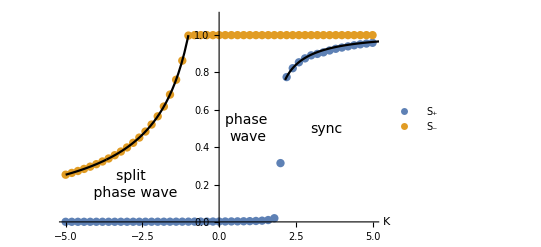

figures/order-pars-undriven.png

```mathematica
{blue,orange}={ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]};

p1b=ListPlot[{dataLower[[All,{1,2}]][[;;;;2]],dataLower[[All,{1,3}]][[;;;;2]]},
AxesLabel->{Style["K",22,Italic]},
PlotLegends->{Style["S_+",19],Style["S_-",19]},
LabelStyle->16,PlotRange->{0,1.1},
PlotStyle->{{PointSize[0.015],blue},{PointSize[0.015],orange}},
Epilog->{Dashed,
Text[Style["sync",14],{3.5,0.5}],
Text[Style["phase \nwave",14],{0.95,0.5}],
Text[Style["split \n phase wave",14],{-2.8,0.2}]
}];
p2b=Plot[1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2),{k,-5,0},PlotRange->{0,1},PlotStyle->Black];
p3b=ListPlot[splusdata[[66;;]],Joined->True,PlotStyle->Black];
pAll3=Show[{p1b,p2b,p3b}]
SetDirectory[NotebookDirectory[]];
Export["figures/order-pars-undriven.png",pAll3]
```

### Hysteresis: S(K) E = 0

#### Data

Computed elsewhere

```mathematica
uu = {0.01,0.035,0.060000000000000005,0.085,0.11000000000000001,0.135,0.16,0.185,0.21,0.235,0.26,0.28500000000000003,0.31000000000000005,0.3350000000000001,0.3600000000000001,0.3850000000000001,0.41000000000000014,0.43500000000000016,0.4600000000000002,0.4850000000000002,0.5100000000000002,0.5350000000000003,0.5600000000000003,0.5850000000000003,0.6100000000000003,0.6350000000000003,0.6600000000000004,0.6850000000000004,0.7100000000000004,0.7350000000000004,0.7600000000000005,0.7850000000000005,0.8100000000000005,0.8350000000000005,0.8600000000000005,0.8850000000000006,0.9100000000000006,0.9350000000000006,0.9600000000000006,0.9850000000000007,1.0100000000000007,1.0350000000000006,1.0600000000000005,1.0850000000000004,1.1100000000000003,1.1350000000000002,1.1600000000000001,1.185,1.21,1.2349999999999999,1.2599999999999998,1.2849999999999997,1.3099999999999996,1.3349999999999995,1.3599999999999994,1.3849999999999993,1.4099999999999993,1.4349999999999992,1.459999999999999,1.484999999999999,1.509999999999999,1.5349999999999988,1.5599999999999987,1.5849999999999986,1.6099999999999985,1.6349999999999985,1.6599999999999984,1.6849999999999983,1.7099999999999982,1.734999999999998,1.759999999999998,1.784999999999998,1.8099999999999978,1.8349999999999977,1.8599999999999977,1.8849999999999976,1.9099999999999975,1.9349999999999974,1.9599999999999973,1.9849999999999972,2.009999999999997,2.034999999999997,2.059999999999997,2.084999999999997,2.1099999999999968,2.1349999999999967,2.1599999999999966,2.1849999999999965,2.2099999999999964,2.2349999999999963,2.2599999999999962,2.284999999999996,2.309999999999996,2.334999999999996,2.359999999999996,2.384999999999996,2.4099999999999957,2.4349999999999956,2.4599999999999955,2.4849999999999954};
SS = {0.005000015641151076,0.017500669982424027,0.03000337613821257,0.042509602207686986,0.055020820503366825,0.06753850919984919,0.08006415411389771,0.09259925049390952,0.10514530484045222,0.11770383676863361,0.13027638091622828,0.14286448890356204,0.15546973135938613,0.16809370001027962,0.18073800985038513,0.19340430139907083,0.20609424305389668,0.21880953355127464,0.23155190454761693,0.24432312332922898,0.2571249956697676,0.2699593688467788,0.28282813483179403,0.29573323367971777,0.3086766571267442,0.3216604524808108,0.3346867264437284,0.34775765003684084,0.36087546275351445,0.3740424778786982,0.38726108786264873,0.4005337701252187,0.41386309361427226,0.4272517252977019,0.44070243791368074,0.45421813219571094,0.4678017751487185,0.4814565491040532,0.4951857255667795,0.5089927427470045,0.5228717551357427,0.5366465964093476,0.5501460508156716,0.5632969431392332,0.576060625075004,0.5884171585845404,0.6003581954904652,0.6118829810035521,0.6229958653422291,0.6337046563869101,0.6440194875568208,0.6539520202502421,0.6635148720214822,0.6727212033902842,0.681584416976412,0.6901179386157716,0.6983350586991057,0.7062488182475127,0.7138719284581536,0.7212167153894183,0.7282950837383362,0.7351184946534352,0.7416979546303476,0.7480440123196209,0.7541667614009526,0.7600758478990438,0.7657804807219504,0.7712894444821968,0.7766111138763818,0.7817534690658793,0.7867241116309382,0.7915302807715594,0.796178869493477,0.8006764406830288,0.8050292426921403,0.8092432246811547,0.8133240513649865,0.8172771172403743,0.821107560241441,0.8248202748079188,0.8284199243610265,0.8319109531900853,0.8352975977590432,0.8385838974465837,0.8417737047367605,0.8448706948793654,0.8478783750407416,0.8508000929666563,0.8536390451792707,0.856398284730317,0.8590807285323896,0.8616891642898366,0.8642262570501762,0.8666945553962857,0.8690964972988563,0.8714344156478085,0.8737105434805336,0.8759270189239844,0.8780858898667981,0.8801891183768176};
```

#### Plot

Transpose::nmtx: The first two levels of {K,{0.00500002,0.0175007,0.0300034,0.0425096,0.0550208,0.0675385,0.0800642,0.0925993,0.105145,0.117704,«90»}} cannot be transposed.

Part::take: Cannot take positions 45 through -1 in Transpose[{K,{0.00500002,0.0175007,0.0300034,0.0425096,0.0550208,0.0675385,0.0800642,0.0925993,0.105145,0.117704,«90»}}].

Transpose::nmtx: The first two levels of {K,{0.00500002,0.0175007,0.0300034,0.0425096,0.0550208,0.0675385,0.0800642,0.0925993,0.105145,0.117704,«90»}} cannot be transposed.

Part::take: Cannot take positions 1 through 45 in Transpose[{K,{0.00500002,0.0175007,0.0300034,0.0425096,0.0550208,0.0675385,0.0800642,0.0925993,0.105145,0.117704,«90»}}].

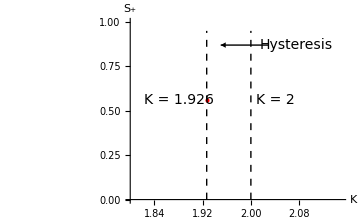

```mathematica
p1a = ListPlot[{{K,SS}ᵀ[[45;;]],{K,SS}ᵀ[[1;;45]],{ab,cd}ᵀ},
PlotRange->{{1.8,2.15},{0,1.0}},
Joined->True,
PlotStyle->{{Thick,blue},{Dotted,blue},{Thick,Thickness[0.01],blue}},
Ticks->{Automatic,Automatic},AxesLabel->{Style["K",18,Italic],Style["S_+",18,Italic]},
LabelStyle->15,AxesStyle->16,ImageSize->Medium,Epilog->{Arrow[{{2.03,0.87},{1.95,0.87}}],
Dashed,Line[{{1.92676,0},{1.92676,0.95}}],Line[{{2,0},{2,0.95}}],
Text[Style["Hysteresis",14],{2.075,0.87}],
Text[Style["K = 1.926",14],{1.88,0.56}],
Text[Style["sync",14],{0.35,0.56}],
Text[Style["K = 2",14],{2.04,0.56}],PointSize->Large,Red,Point[{1.92676,0.563297}]
}]

SetDirectory[NotebookDirectory[]];
Export["figures/order-par-hysteresis.png",p1a];
```

### Hystersis in S(E) fixed K

## S(K) with E > 0

### Data

```mathematica
data1 = {{1.,0.010064308327690214,1.},{1.02,0.010272401849889347,1.},{1.04,0.010489282710918686,1.},{1.06,0.010715519568599204,1.},{1.08,0.010951731234897125,1.},{1.1,0.011198592330855585,1.},{1.12,0.011456839724458153,1.},{1.1400000000000001,0.011727279880927196,1.},{1.16,0.012010797280000252,1.},{1.18,0.012308364085441212,1.},{1.2,0.01262105128970524,1.},{1.22,0.012950041603290583,1.},{1.24,0.013296644416069243,1.},{1.26,0.01366231323004897,1.},{1.28,0.01404866605359447,1.},{1.3,0.014457509361414921,1.},{1.32,0.014890866369972972,1.},{1.34,0.015351010563669821,1.},{1.3599999999999999,0.015840505646593016,1.},{1.38,0.016362253405018,1.},{1.4,0.016919551372094298,1.},{1.42,0.01751616272168683,1.},{1.44,0.018156401531185837,1.},{1.46,0.018845237510605618,1.},{1.48,0.019588425594951622,1.},{1.5,0.020392667580316957,1.},{1.52,0.021265815460423082,1.},{1.54,0.022217129603023248,1.},{1.56,0.023257609871700485,1.},{1.58,0.0244004249873404,1.},{1.6,0.02566147600266962,1.},{1.62,0.027060145614730607,1.},{1.6400000000000001,0.028620309270357105,1.},{1.6600000000000001,0.030371721885614062,1.},{1.6800000000000002,0.03235195465826226,1.},{1.7000000000000002,0.03460915636858828,1.},{1.72,0.037206083449740426,1.},{1.74,0.04022614269062609,1.},{1.76,0.04378274173588257,1.},{1.78,0.048034308268807564,1.},{1.8,0.05320953778255582,1.},{1.82,0.05965224664082599,1.},{1.8399999999999999,0.06790739432026022,1.},{1.8599999999999999,0.07890052602303303,1.},{1.88,0.09438008646483824,1.},{1.9,0.11820508157386694,1.},{1.92,0.16093122707494098,1.},{1.94,0.29024915683139846,1.},{1.96,0.6840929937058858,1.},{1.98,0.6983755844773261,1.},{2.,0.7109096983487134,1.},{2.02,0.7205768746258174,1.},{2.04,0.7280004872881131,1.},{2.06,0.7409488120272457,1.},{2.08,0.7477813775480336,1.},{2.1,0.7504763165199657,1.},{2.12,0.7644012590241256,1.},{2.14,0.7710312470770527,1.},{2.16,0.7766014346552481,1.},{2.1799999999999997,0.7829294890970437,1.},{2.2,0.7875081770688257,1.},{2.2199999999999998,0.7933307899768421,1.},{2.24,0.7970970163743162,1.},{2.26,0.8006356897820692,1.},{2.2800000000000002,0.807955020814107,1.},{2.3,0.8132206062085812,1.},{2.3200000000000003,0.8158675714039999,1.},{2.34,0.8201075254871552,1.},{2.3600000000000003,0.8252840351496353,1.},{2.38,0.827961222951174,1.},{2.4000000000000004,0.8316620324103274,1.},{2.42,0.8244500285783373,1.},{2.44,0.8382141744919833,1.},{2.46,0.8370677484753001,1.},{2.48,0.8446798627355349,1.},{2.5,0.8486761911131038,1.},{2.52,0.8517307864662333,1.},{2.54,0.8534986827785083,1.},{2.56,0.8557529114523393,1.},{2.58,0.8417218158778556,1.},{2.6,0.8602846724729709,1.},{2.62,0.8628065540036711,1.},{2.64,0.8527539291560815,1.},{2.66,0.8579677589968159,1.},{2.6799999999999997,0.86909269664843,1.},{2.7,0.8609654691435512,1.},{2.7199999999999998,0.8744293698800147,1.},{2.74,0.8760248220464091,1.},{2.76,0.8760727483893365,1.},{2.7800000000000002,0.8814847121068486,1.},{2.8,0.8813505002649947,1.},{2.8200000000000003,0.8805830519836544,1.},{2.84,0.8648910103336331,1.},{2.8600000000000003,0.8890791080523919,1.},{2.88,0.8813676748279855,1.},{2.9000000000000004,0.8564925452084674,1.},{2.92,0.8807014546580435,1.},{2.94,0.8948607347501135,1.},{2.96,0.8950608906069062,1.},{2.98,0.8823655225465028,1.},{3.,0.8907695545637851,1.}};


data3={{1.,0.011289177820275668,1.},{1.02,0.011580517959117907,1.},{1.04,0.011887295608875748,1.},{1.06,0.012210771432308249,1.},{1.08,0.01255234724204278,1.},{1.1,0.012913586332869778,1.},{1.12,0.013296237434905264,1.},{1.1400000000000001,0.013702263063428033,1.},{1.16,0.014133873237390956,1.},{1.18,0.014593565792463636,1.},{1.2,0.01508417484537906,1.},{1.22,0.015608929401702231,1.},{1.24,0.016171524676260932,1.},{1.26,0.01677620946837344,1.},{1.28,0.017427893978951243,1.},{1.3,0.01813228388496593,1.},{1.32,0.01889604846153664,1.},{1.34,0.019727033306939326,1.},{1.3599999999999999,0.020634532149029963,1.},{1.38,0.021629637861260494,1.},{1.4,0.022725701083294716,1.},{1.42,0.02393893715170581,1.},{1.44,0.025289240738195242,1.},{1.46,0.02680129658950606,1.},{1.48,0.028506120840435644,1.},{1.5,0.030443242596733637,1.},{1.52,0.03266386212748418,1.},{1.54,0.03523554286302481,1.},{1.56,0.03824939576698526,1.},{1.58,0.04183147944368859,1.},{1.6,0.04616168671189261,1.},{1.62,0.05150676176758797,1.},{1.6400000000000001,0.058281946560328354,1.},{1.6600000000000001,0.06717782738883313,1.},{1.6800000000000002,0.07945315891981855,1.},{1.7000000000000002,0.097783783383237,1.},{1.72,0.12922451146304473,1.},{1.74,0.22833360385865442,1.},{1.76,0.7447031685405651,1.},{1.78,0.7555276321400527,1.},{1.8,0.7632448744760774,1.},{1.82,0.7733002939303487,1.},{1.8399999999999999,0.776765206268136,1.},{1.8599999999999999,0.7889093213883737,1.},{1.88,0.7918978457874701,1.},{1.9,0.7991208274613287,1.},{1.92,0.8084268081571676,1.},{1.94,0.8145418623636752,1.},{1.96,0.8168442100851464,1.},{1.98,0.8244105059625434,1.},{2.,0.8302495765513602,1.},{2.02,0.8316740901419659,1.},{2.04,0.8397908421893864,1.},{2.06,0.8428000415422763,1.},{2.08,0.847309055180839,1.},{2.1,0.8502088787374391,1.},{2.12,0.8549606319619596,1.},{2.14,0.8580364049325241,1.},{2.16,0.8605744480379018,1.},{2.1799999999999997,0.8609446022109014,1.},{2.2,0.8663427072111759,1.},{2.2199999999999998,0.8699085284127207,1.},{2.24,0.8714195315819058,1.},{2.26,0.8766032050609385,1.},{2.2800000000000002,0.878247426316602,1.},{2.3,0.8802525469222753,1.},{2.3200000000000003,0.8830091438111607,1.},{2.34,0.8840850398480412,1.},{2.3600000000000003,0.8871228499129147,1.},{2.38,0.8894549471639741,1.},{2.4000000000000004,0.8909870210093918,1.},{2.42,0.8949164259949526,1.},{2.44,0.8960855996561149,1.},{2.46,0.8970519019532479,1.},{2.48,0.9003981399353613,1.},{2.5,0.9019313689524294,1.},{2.52,0.9039866480290494,1.},{2.54,0.9049001495830246,1.},{2.56,0.904975908482234,1.},{2.58,0.9064898018046323,1.},{2.6,0.9088287017789516,1.},{2.62,0.9111088338876565,1.},{2.64,0.9107670464678083,1.},{2.66,0.9135757375080142,1.},{2.6799999999999997,0.9143086157820574,1.},{2.7,0.9099504461551065,1.},{2.7199999999999998,0.9171359120641376,1.},{2.74,0.9170330161766317,1.},{2.76,0.9200331532897317,1.},{2.7800000000000002,0.9216748485736976,1.},{2.8,0.9226344757082161,1.},{2.8200000000000003,0.9258136779930944,1.},{2.84,0.9257644512188733,1.},{2.8600000000000003,0.9263580786512037,1.},{2.88,0.9265840383667843,1.},{2.9000000000000004,0.9294220481593609,1.},{2.92,0.9295231104915346,1.},{2.94,0.9294050881800414,1.},{2.96,0.9215728248478193,1.},{2.98,0.9326814037367439,1.},{3.,0.921814407537323,1.}};

bb1={-0.013453844807920352,-0.15579681842580095,-1.1041946772704194,7.382542821371025,2.486047224850774,2.075128424297635,1.9702805077271344,1.9354760162084141,1.9185268195514789,1.9037811827958777,1.8999445788904334,1.916760419071296,1.9502693490242529,1.996256965844945,2.0515669341311242,2.1139512876540487,2.1818077596374956,2.253977422751481,2.3296064351792216,2.4080538361449944,2.48882982993586,2.571553923728505,2.655926056255254,2.7417063367697607,2.8287005821055633,2.9167498237621197,3.0057225784592227,3.0955090729789134,3.1860168719184667,3.277167526822606};

aa1={-7.4328194971544095,-1.2837232622645054,-0.2716912209191255,0.05418187332988815,0.20112248673394073,0.28913873135494295,0.35527936111366304,0.4133350107676328,0.46910993937025375,0.5252704507413021,0.5789642562323577,0.6260563334156394,0.6665745942479219,0.7013125183547849,0.7311484578178179,0.7568764755102734,0.7791703886333473,0.7985883007659855,0.8155884063969928,0.8305462153627597,0.8437700218556606,0.8555138508665658,0.865987964756408,0.8753672732243258,0.8837980293195642,0.891403156629469,0.8982864950178006,0.9045361954973906,0.9102274459249051,0.9154246694579774};

bb3={1.6687999988854099,1.6962954205042517,1.7397417250124674,1.7943900816775344,1.857148735636979,1.9259499331159018,1.9993703348999776,2.0764026043005237,2.156315404743781,2.2385654390914222,2.3227407260224986,2.408523082265144,2.495662711127092,2.583960609208072,2.673256138162335,2.763418082233843,2.8543381046498966,2.9459258850647885,3.038105454811077,3.1308123988403525,3.2239916937228053};

aa3={0.5992329821835446,0.6484719505244004,0.6897575558184653,0.724480152489842,0.7538437676720695,0.7788364454382376,0.8002519453606095,0.8187236889797095,0.834757288307682,0.8487578548390184,0.8610517642340716,0.8719036223746769,0.8815293790267181,0.8901064481415998,0.8977815353113984,0.9046767176029678,0.9108941914640166,0.9165200026546565,0.921626994733176,0.9262771544772713,0.9305234892016252};
```

### Plot

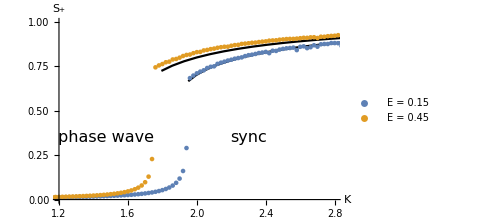

```mathematica
p=ListPlot[{data1[[All,{1,2}]],data3[[All,{1,2}]],{bb1[[13;;-1]],aa1[[13;;-1]]}ᵀ,{bb3[[4;;-1]],aa3[[4;;-1]]}ᵀ},
PlotStyle->{Automatic,Automatic,Black,Black},
Joined->{False,False,True,True},
AxesLabel->{Style["K",18,Italic],Style["S_+",18,Italic]},
LabelStyle->16,PlotStyle->{ColorData[99,"ColorList"]},
PlotRange->{{1.2,2.8},{0,1}},
PlotLegends->{"E = 0.15", "E = 0.45"},
ImageSize->Medium,
Epilog->{
Text[Style["phase wave",16],{1.475,0.35}],
Text[Style["sync",16],{2.3,0.35}]
}]

SetDirectory[NotebookDirectory[]];
Export["figures/s-versus-k-different.e.png",p];
```

## E > 0 J = k -- pictures

$Aborted

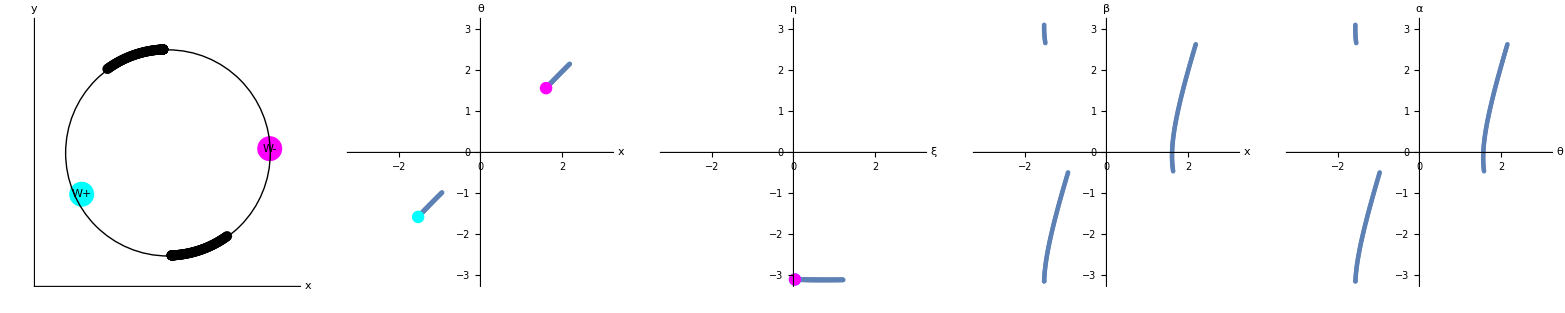

```mathematica
(*Preamble*)
{dt,n,T}={0.1,200,400}; 
{J,k}={3,3};
{e,b}={0.7,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]
results=plotResults[znew,pin]
```

```mathematica
size=25;
```

### Pinned state

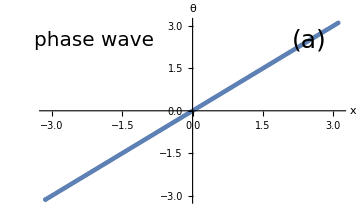

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={1,1};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p1=ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["phase wave",20],{-2.1,2.5}],Text[Style["(a)",25],{2.5,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

### Sync state

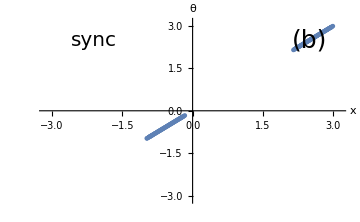

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,200}; 
{J,k}={3,3};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p2= ListPlot[{Mod[x,2π]-1.5π,Mod[θ,2π]-1.5π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["sync",20],{-2.1,2.5}],Text[Style["(b)",25],{2.5,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

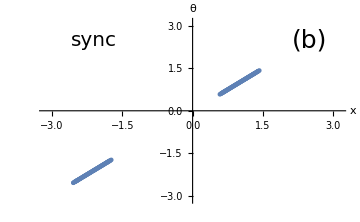

```mathematica
{x,θ}=z1;
p2= ListPlot[{Mod[x,2π]-1.5π,Mod[θ,2π]-1.5π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["sync",20],{-2.1,2.5}],Text[Style["(b)",25],{2.5,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={3,3};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{-0.25π,-0.5π}],{i,1,2},{j,1,n}],Table[RandomReal[{0.5π,1.0π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p4= ListPlot[{Mod[x,2π]-1.2π,Mod[θ,2π]-1.2π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,LabelStyle->15,ImageSize->Medium,PlotRange->{{-π,π},{-π,π}},
Epilog->{Text[Style["sync",20],{-2.1,2.5}],Text[Style["(c)",25],{2.5,2.5}]}]
```

-Graphics-

### Flipped phase wave

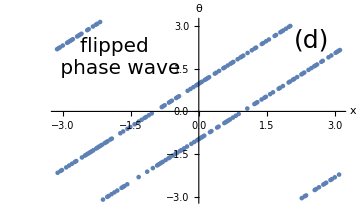

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={-2,-2};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p3= ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["flipped \n phase wave",20],{-1.8,1.9}],Text[Style["(d)",25],{2.5,2.5}]}]
```

### Plot together

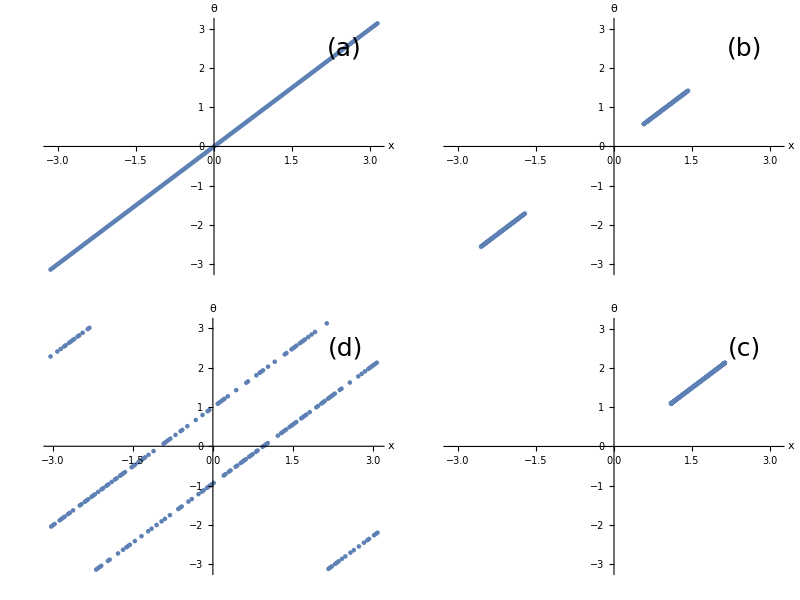

```mathematica
pAll=Grid[{{p1,p2},{p3,p4}}]
SetDirectory[NotebookDirectory[]];
Export["states-undriven.png",pAll];
```

```mathematica
pAll=Grid[{{p1,p2,p4,p3}}]
SetDirectory[NotebookDirectory[]];
Export["figures/states-undriven.png",pAll];
```

-Graphics-

### S(K)

#### Make data

```mathematica
data=ParallelTable[
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.5,200,200}; 
{J,k}={K,K};
{e,b}={0.75,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

cutoff=Round[0.5 Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
If[Sp≤Sm,{Sp,Sm}={Sm,Sp}];
{K,Sp,Sm},
{K,-5,5,0.5}
];
```

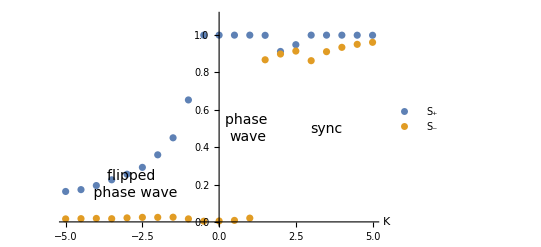

figures/order-pars-driven.png

```mathematica
p1c=ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{Style["K",22,Italic]},PlotLegends->{Style["S_+",19],Style["S_-",19]},LabelStyle->16,PlotRange->{0,1.1},Epilog->{Dashed,(*Line[{{-1,0},{-1,1}}],Line[{{2,0},{2,1}}],*)Text[Style["sync",14],{3.5,0.5}],Text[Style["phase \nwave",14],{0.95,0.5}],Text[Style["flipped \n phase wave",14],{-2.8,0.2}]}]
SetDirectory[NotebookDirectory[]];
Export["figures/order-pars-driven.png",p1b]
```

### S(E)

#### Make data

```mathematica
data=ParallelTable[
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.25,400,200}; 
{J,k}={-1.2,-1.2};
{e,b}={e1,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

cutoff=Round[0.5 Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
{e1,Sp,Sm},
{e1,0,2,0.05}
];
```

#### Plot

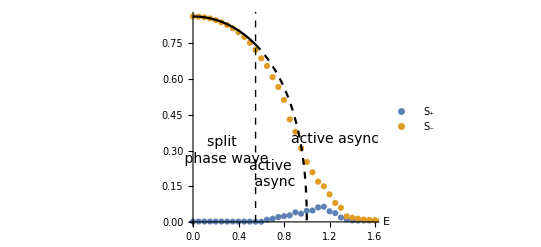

figures/order-pars-driven-versus-e.png

```mathematica
data={{0.,0.0015431891743105208,0.8634289040561737},{0.05,0.001542231026925399,0.8624952520869016},{0.1,0.0015333824954305438,0.8596406307222428},{0.15000000000000002,0.0015276018506453477,0.8549027821690558},{0.2,0.001526159452115723,0.8480423619687383},{0.25,0.0015086980965025945,0.8390652740530423},{0.30000000000000004,0.0014627721204739721,0.8277553230062077},{0.35000000000000003,0.0014197530263105264,0.8138732485082064},{0.4,0.001342266681533793,0.797096865324931},{0.45,0.001335381301520938,0.7769932065185733},{0.5,0.0011937149774600099,0.7527190237646557},{0.55,0.0010293523051918658,0.7234197499996501},{0.6000000000000001,0.0008421410108058913,0.6872987274298573},{0.6500000000000001,0.009135672324139966,0.655222107325316},{0.7000000000000001,0.013306923328251912,0.6085603254515343},{0.7500000000000001,0.0204238052760879,0.567103666490758},{0.8,0.024274246587567803,0.5124869557372679},{0.8500000000000001,0.027515170114563323,0.4306820720791643},{0.9,0.04000473985197091,0.3784931687424766},{0.9500000000000001,0.03450477098427826,0.30930483548323673},{1.,0.04675800707017197,0.25196514056246894},{1.05,0.04783535640094325,0.2085558777335371},{1.1,0.06076693736705923,0.1690633686450241},{1.1500000000000001,0.06374807613269524,0.14961295051468065},{1.2000000000000002,0.04442151903911222,0.11586921420975933},{1.2500000000000002,0.03686876423203032,0.07950772572040031},{1.3,0.018498623834229736,0.05938696433270239},{1.35,0.010209204112681183,0.023393461609763338},{1.4000000000000001,0.006459895068271312,0.017878889323096003},{1.4500000000000002,0.005890592997765998,0.013374506238840003},{1.5000000000000002,0.006081770008738943,0.010070875968162894},{1.5500000000000003,0.0060176967929368354,0.008487004047693208},{1.6,0.005733658416643102,0.0074120432973171085},{1.6500000000000001,0.0055034741837855115,0.006727158302764834},{1.7000000000000002,0.005316016867950638,0.006383409079559668},{1.75,0.0051179264088491785,0.006296574952071218},{1.8,0.004889013365800701,0.006336799766739144},{1.85,0.0046308220892436035,0.0064141009117347075},{1.9000000000000001,0.0043566208633540136,0.006476918029961915},{1.9500000000000002,0.00409039945232664,0.006459723375243968},{2.,0.003849079959091887,0.0064567198361088155}};

p1c=ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},
AxesLabel->{Style["E",22,Italic]},
PlotLegends->{Style["S_+",19],Style["S_-",19]},
LabelStyle->16,
PlotRange->{{0,1.6},All},
AxesOrigin->{0,0},
Epilog->{
Dashed,
Line[{{0.55,0},{0.55,1}}],
Text[Style["active async",14],{1.25,0.35}],
Text[Style["active \n async",14],{0.70,0.20}],
Text[Style["split \n phase wave",14],{0.275,0.3}],
Text[Style["flipped \n phase wave",14],{-2.8,0.2}]
}];

(*Analytic solution*)
Clear[e]
ssol=Solve[k^2 s^3+k^2 s^2-2+2 e^2==0,s];
p2c=Plot[s/.ssol/.k->-1.2/.e->e2,{e2,0,0.55},PlotStyle->Black];
p3c=Plot[s/.ssol/.k->-1.2/.e->e2,{e2,0.55,1},PlotStyle->{Black,Dashed}];
p4c=Show[{p1c,p2c,p3c}]

SetDirectory[NotebookDirectory[]];
Export["figures/order-pars-driven-versus-e.png",p4c]
```

## Flying saucers

### Wave speed

#### Make data

```mathematica
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.5,200,500}; 
{J,k}={1,2};
{e,b}={1.5,0.75};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
]
```

#### Plot of order parameters

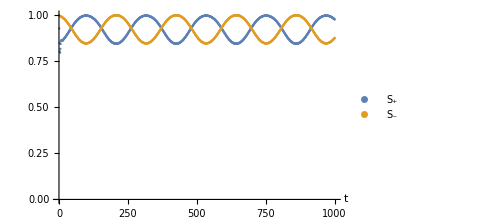
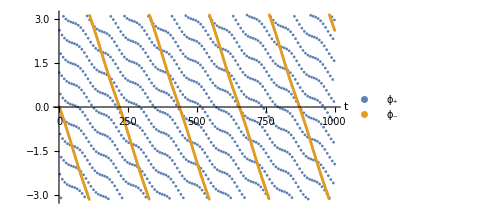
-Graphics- | -Graphics-

```mathematica
p1=ListPlot[{Wp//Abs,Wm//Abs},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1},ImageSize->Medium];
p2=ListPlot[{Wp//Arg,Wm//Arg},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},LabelStyle->15,PlotRange->All,ImageSize->Medium];
```

#### Measure wave speed S(E), Ω(E)

```mathematica
{ϕp,ϕm}={Wp//Arg,Wm//Arg};
ListPlot[{ϕp,ϕm}]
```

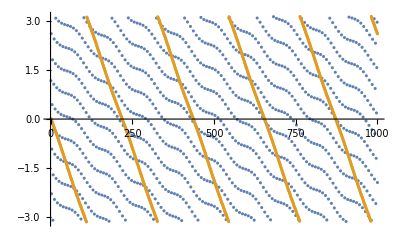

```mathematica
findWaveSpeed[ϕ_,dt_]:=Block[{vel,index,data},
index=Round[0.25*Length[ϕ]];
data=ϕ[[index;;-1]];
vel=Differences[data]/dt;
Return[Median[vel]]
]
```

```mathematica
findWaveSpeed[ϕp,dt]
```

2.76835

```mathematica
data=ParallelTable[
{dt,n,T}={0.1,500,200};
{J,k,b}={1,2,0.75};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{ϕp,ϕm}={Wps//Arg,Wms//Arg};
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{Ωp, Ωm}={findWaveSpeed[ϕp,dt]//Abs,findWaveSpeed[ϕm,dt]//Abs};
If[Ωp<Ωm,{Ωp,Ωm}={Ωm,Ωp}];
{e,Sp,Sm,Ωp,Ωm},
{e,0,0.8,0.025}
];
```

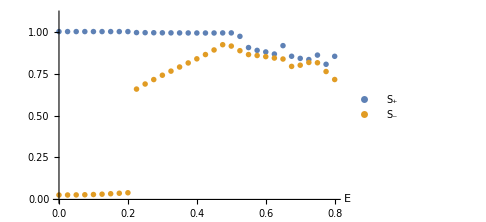

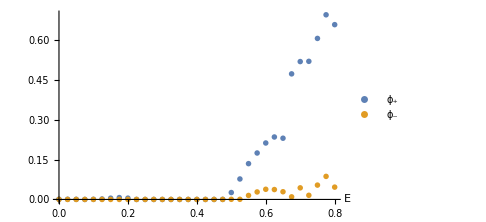

```mathematica
p3=ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1},ImageSize->Medium]
p4=ListPlot[{data[[All,{1,4}]],data[[All,{1,5}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},PlotRange->All,LabelStyle->15,ImageSize->Medium]
```

#### Plot together

```mathematica
pAll=Grid[{{p1,p2},{p3,p4}}]
SetDirectory[NotebookDirectory[]];
Export["figures/flying-saucers.png",pAll]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

figures/flying-saucers.png

## Sliding phase waves

#### Make data

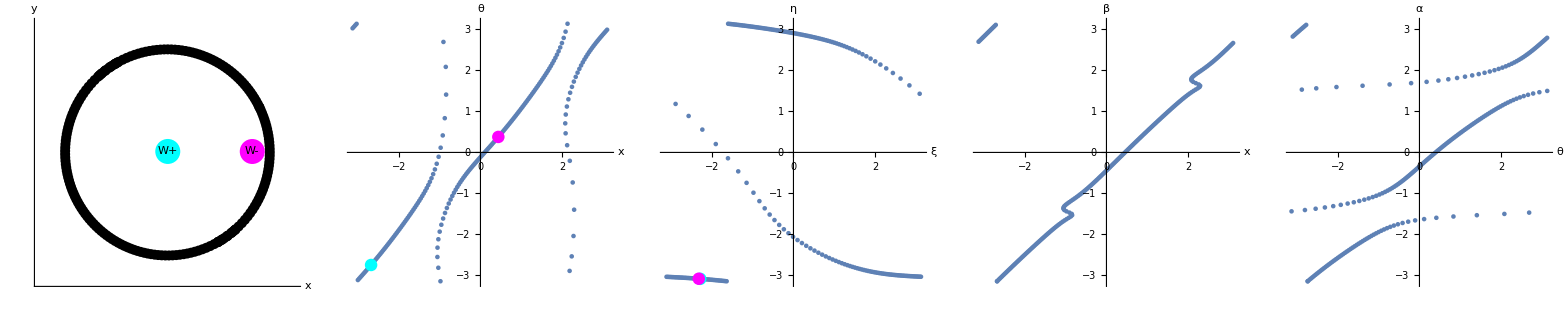

```mathematica
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.5,200,500}; 
{J,k}={1,-5};
{e,b}={0.9,2};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ;
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];
plotResults[znew,pin]
```

#### Make pics

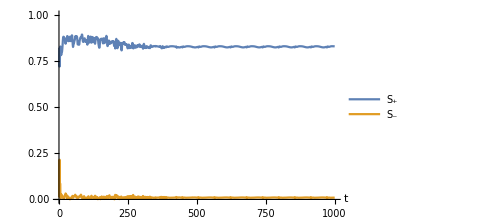
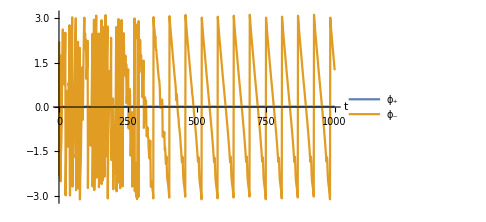
-Graphics- | -Graphics-

```mathematica
p1=ListPlot[{Wm//Abs,Wp//Abs},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1},ImageSize->Medium,Joined->True];
p2=ListPlot[{Wm//Arg,Wp//Arg},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},LabelStyle->15,PlotRange->All,ImageSize->Medium,Joined->True];
Grid[{{p1,p2}}]
```

#### Measure wave speed S(E), Ω(E)

```mathematica
data=ParallelTable[
{dt,n,T}={0.25,300,300};
{J,k,b}={1,-5,2};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{ϕp,ϕm}={Wps//Arg,Wms//Arg};
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{Ωp, Ωm}={findWaveSpeed[ϕp,dt]//Abs,findWaveSpeed[ϕm,dt]//Abs};
If[Ωp<Ωm,{Ωp,Ωm}={Ωm,Ωp}];
{e,Sp,Sm,Ωp,Ωm},
{e,0,4,0.025}
];
```

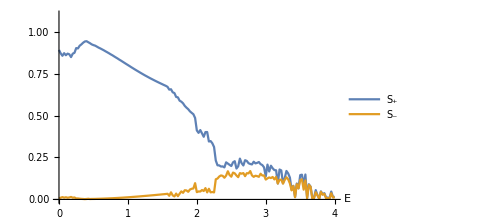

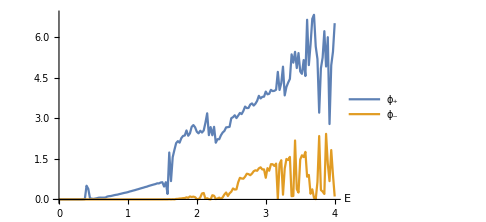

```mathematica
p3=ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1},ImageSize->Medium,Joined->True]
p4=ListPlot[{data[[All,{1,4}]],data[[All,{1,5}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},PlotRange->All,LabelStyle->15,ImageSize->Medium,Joined->True]
```

#### Plot together

```mathematica
pAll=Grid[{{p1,p3},{p2,p4}}]
SetDirectory[NotebookDirectory[]];
Export["figures/sliding-phase-wave.png",pAll]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

figures/sliding-phase-wave.png

## Messy phase waves

#### Make data

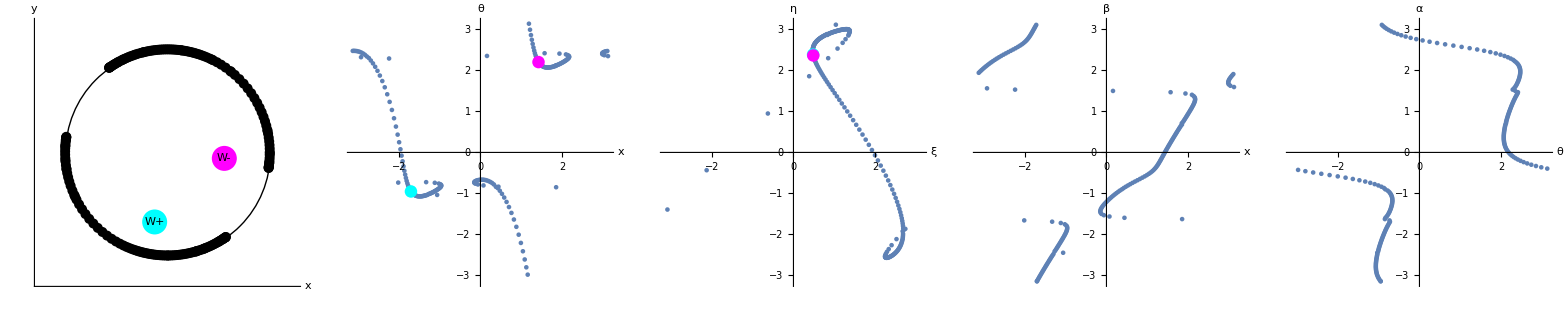

```mathematica
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.25,200,200}; 
{J,k}={1,2};
{e,b}={1.9,2};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ;
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];
plotResults[znew,pin]
```

#### Make pics

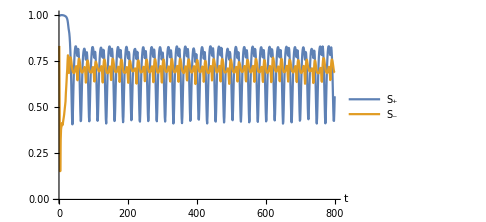
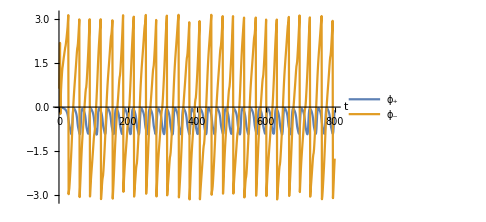
-Graphics- | -Graphics-

```mathematica
p1=ListPlot[{Wm//Abs,Wp//Abs},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1},ImageSize->Medium,Joined->True];
p2=ListPlot[{Wm//Arg,Wp//Arg},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},LabelStyle->15,PlotRange->All,ImageSize->Medium,Joined->True];
Grid[{{p1,p2}}]
```

#### Measure wave speed S(E), Ω(E)

```mathematica
data=ParallelTable[
{dt,n,T}={0.25,300,300};
{J,k,b}={1,2,2};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{ϕp,ϕm}={Wps//Arg,Wms//Arg};
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{Ωp, Ωm}={findWaveSpeed[ϕp,dt]//Abs,findWaveSpeed[ϕm,dt]//Abs};
If[Ωp<Ωm,{Ωp,Ωm}={Ωm,Ωp}];
{e,Sp,Sm,Ωp,Ωm},
{e,0,3.5,0.025}
];
```

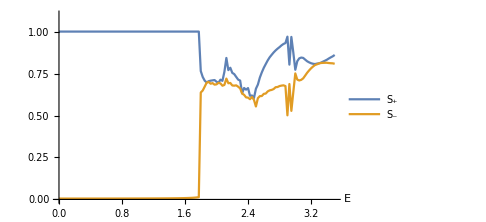

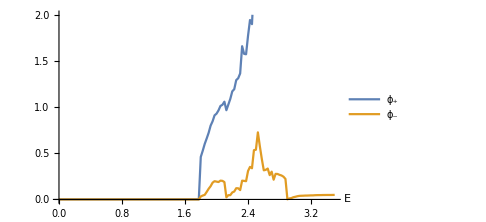

```mathematica
p3=ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1},ImageSize->Medium,Joined->True]
p4=ListPlot[{data[[All,{1,4}]],data[[All,{1,5}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},PlotRange->{0,2},LabelStyle->15,ImageSize->Medium,Joined->True]
```

#### Plot together

```mathematica
pAll=Grid[{{p1,p3},{p2,p4}}]
SetDirectory[NotebookDirectory[]];
Export["figures/messy-phase-wave.png",pAll]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

figures/messy-phase-wave.png

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[Mod[{x+θ,x-θ}ᵀ,2π],PlotRange->{{0,2π},{0,2π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin,x1,θ1,x2,θ2,ξ1,ξ2,η1,η2,index,n},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
n=Length[x];
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}];

(*Scatter plot in (ξ,θ) space*)
{ξ1,η1}={x[[1]]+θ[[1]],x[[1]]-θ[[1]]};
{ξ2,η2}={x[[index]]+θ[[index]],x[[index]]-θ[[index]]};
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]},Epilog->{Cyan,PointSize[0.025],Point[{ξ1,η1}//mod],Magenta,Point[{ξ2,η2}//mod]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];

findWaveSpeed[ϕ_,dt_]:=Block[{vel,index,data},
index=Round[0.25*Length[ϕ]];
data=ϕ[[index;;-1]];
vel=Differences[data]/dt;
Return[Median[vel]]
];

findVmean[xs_,thetas_]:=Module[{vx,vtheta,tcutoff,vxMean,vthetaMean,vMean},
{vx,vtheta}={{},{}};
tcutoff=Round[0.9Dimensions[xs][[2]]];
vxMean=Table[Mean[Differences[xs[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vthetaMean=Table[Mean[Differences[thetas[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vMean=√(vxMean^2+vthetaMean^2);
Return[vMean]
]
```